# Holiday 2024 Biomedicine Results - Merry Christmas!

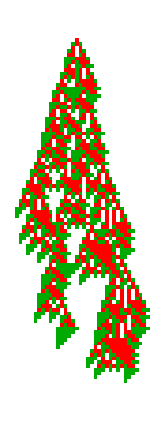

```mathematica
PlotCA[{6006804516645,3,1}, "steps"->94,ColorRules->{1->Red, 2->Darker@Green}]
```

### Init

```mathematica
k4rob =Select[ , Last[#]>100&];
k4reg= Select[,Last[#]>100&];
```

```mathematica
psrob = Import["/Users/erichegonzales/Projects/Wolfram/CAEvolution/Biomed/Output/psrob1.csv"];
```

```mathematica
msrob = N[Mean/@ psrob];
```

```mathematica
psreg = Import["/Users/erichegonzales/Projects/Wolfram/CAEvolution/Biomed/Output/psreg1.csv"];
```

```mathematica
msreg = N[Mean/@ psreg];
```

```mathematica
sirob = SortBy[Range[Length[k4rob]], msrob[[#]]&];
```

```mathematica
sireg = SortBy[Range[Length[k4reg]], msreg[[#]]&];
```

```mathematica
ru = k4rob[[sirob[[15]],1]];
{n, k, r} = ru;
pat = getca[ru, 200];
ca = pat;
```

### The Two Types of Robustness

A big question from our last meeting was how are these robust automata different from the regular ones? We can get at this by looking at the perturbation sensitivity to all possible single point perturbations, with warmer colors representing higher changes in lifetime:

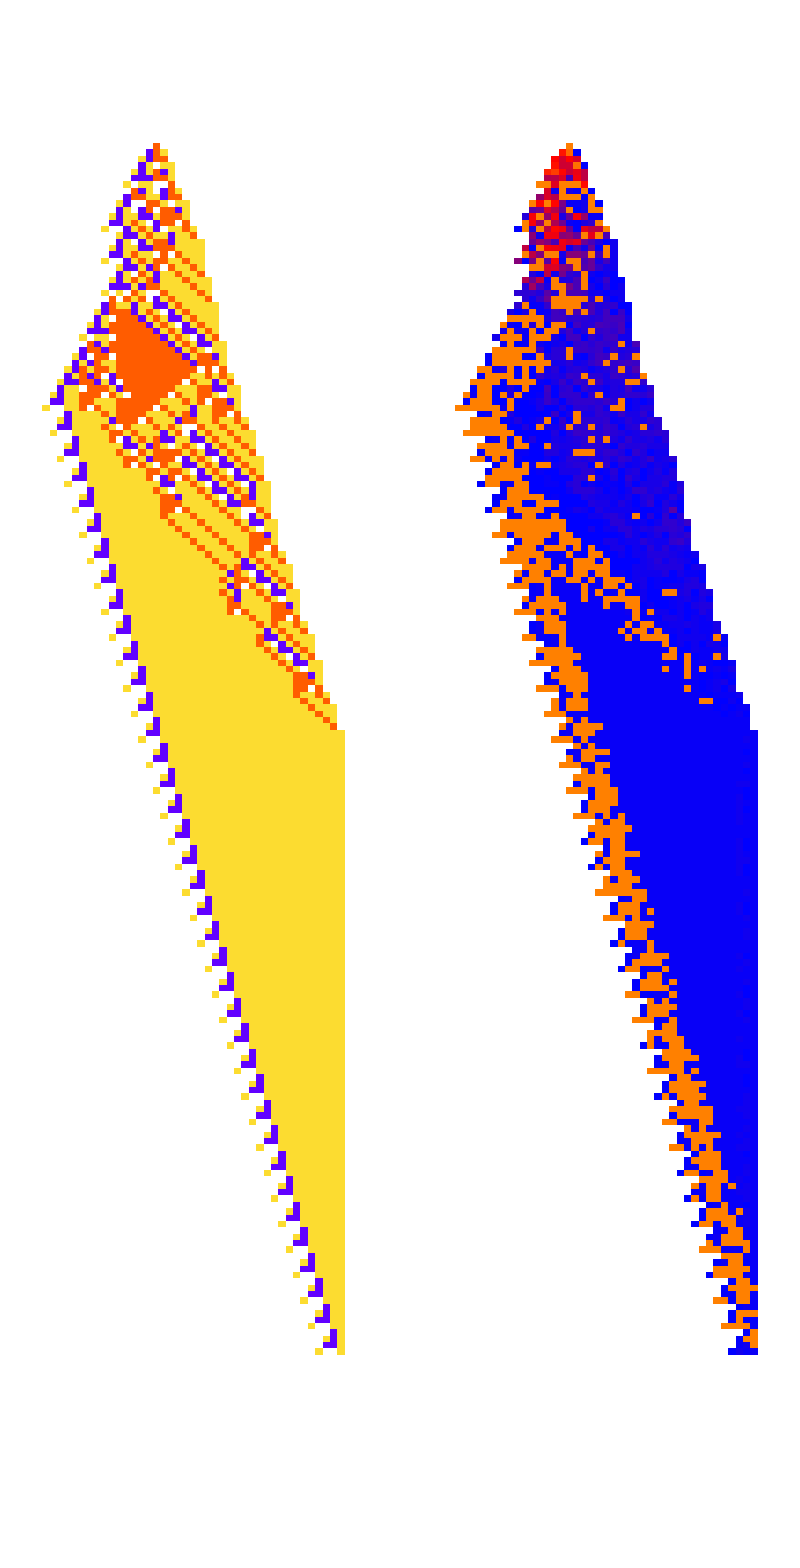

```mathematica
GraphicsRow@{PlotCA[getca[#[[1]], 200]], PerturbationSensitivityPlot[{ getca[#[[1]], 200],#[[1]]}]}&@k4rob[[sirob[[15]]]]
```

Other automata also develop pockets of “protective tissue”:

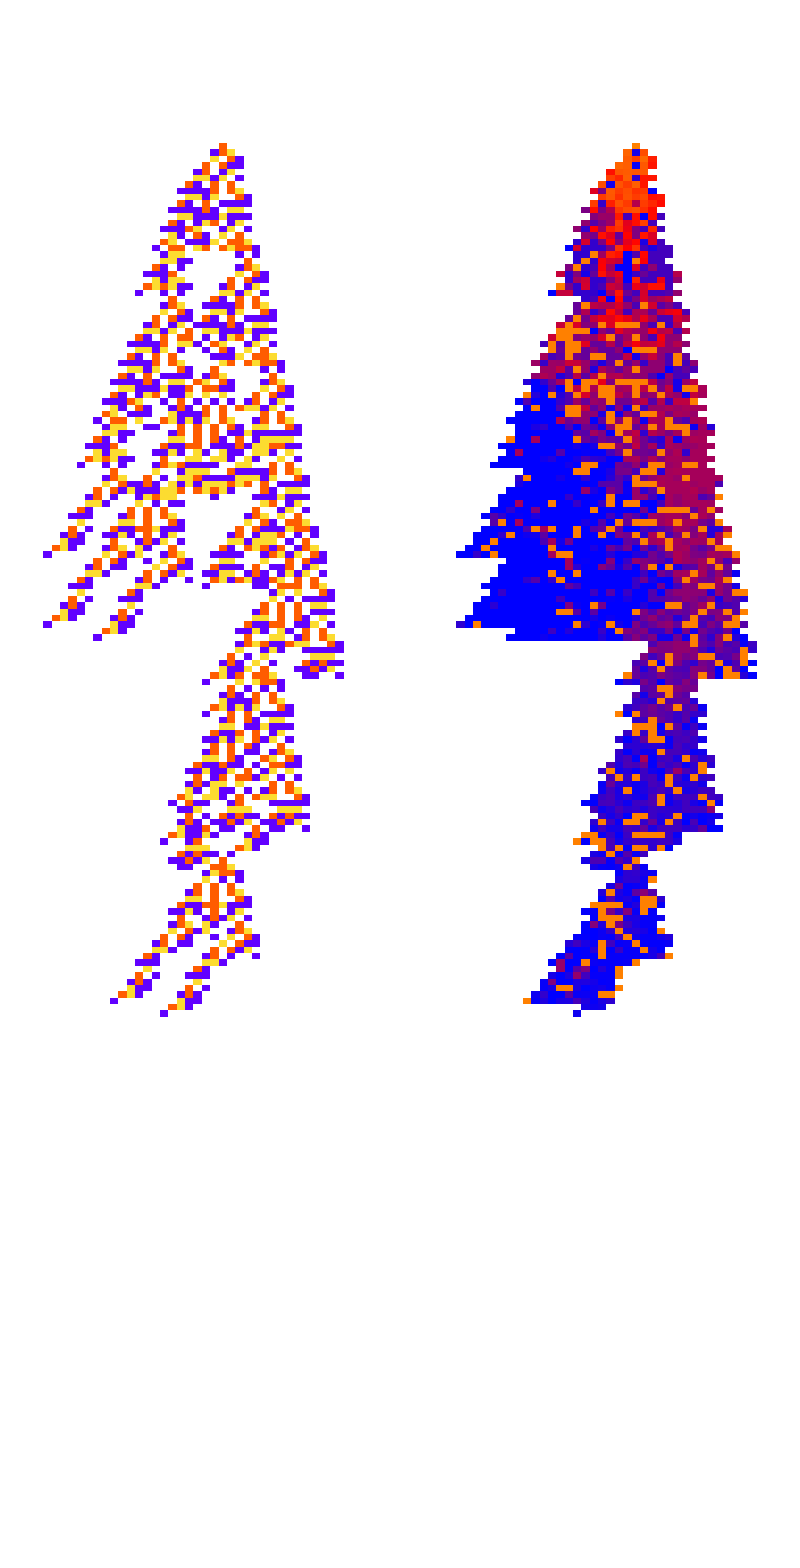

```mathematica
GraphicsRow@({PlotCA[getca[#[[1]], 200]], PerturbationSensitivityPlot[{ getca[#[[1]], 200],#[[1]]}]}&@k4rob[[sirob[[6]]]])
```

When “skin” on the left is perturbed right leg remains unperturbed, and most of the time the lifetime remains the same:

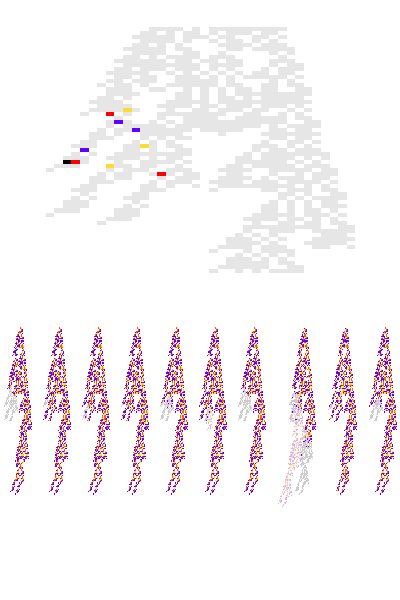

```mathematica
With[{ru =k4rob[[sirob[[6]], 1]],ca = getca[k4rob[[sirob[[6]], 1]] , 200], prus = Table[RandomInteger[{50, 70}]->{RandomSample[Range[1, 10, 1], 1], "Enumerate"}, 10]},
pcasperts = PerturbCA[{ca, ru}, #, "ReturnPerturbations"->True]&/@ prus;
Column@{HighlightPerturbations[ca, Flatten[pcasperts[[All, 2]], 1], "Span"->30;;90, ImageSize->Small],
GraphicsRow[PlotDifferences[ca, #[[1]]]&/@ pcasperts]}]
```

#### Irreducible Robustness

But with some rules, it’s not so easy to see why they are robust. This rule here is the most robust (by mean change in lifetime) but it doesn’t seem to be using skin, illustrated by the random spread of blue across the automata.

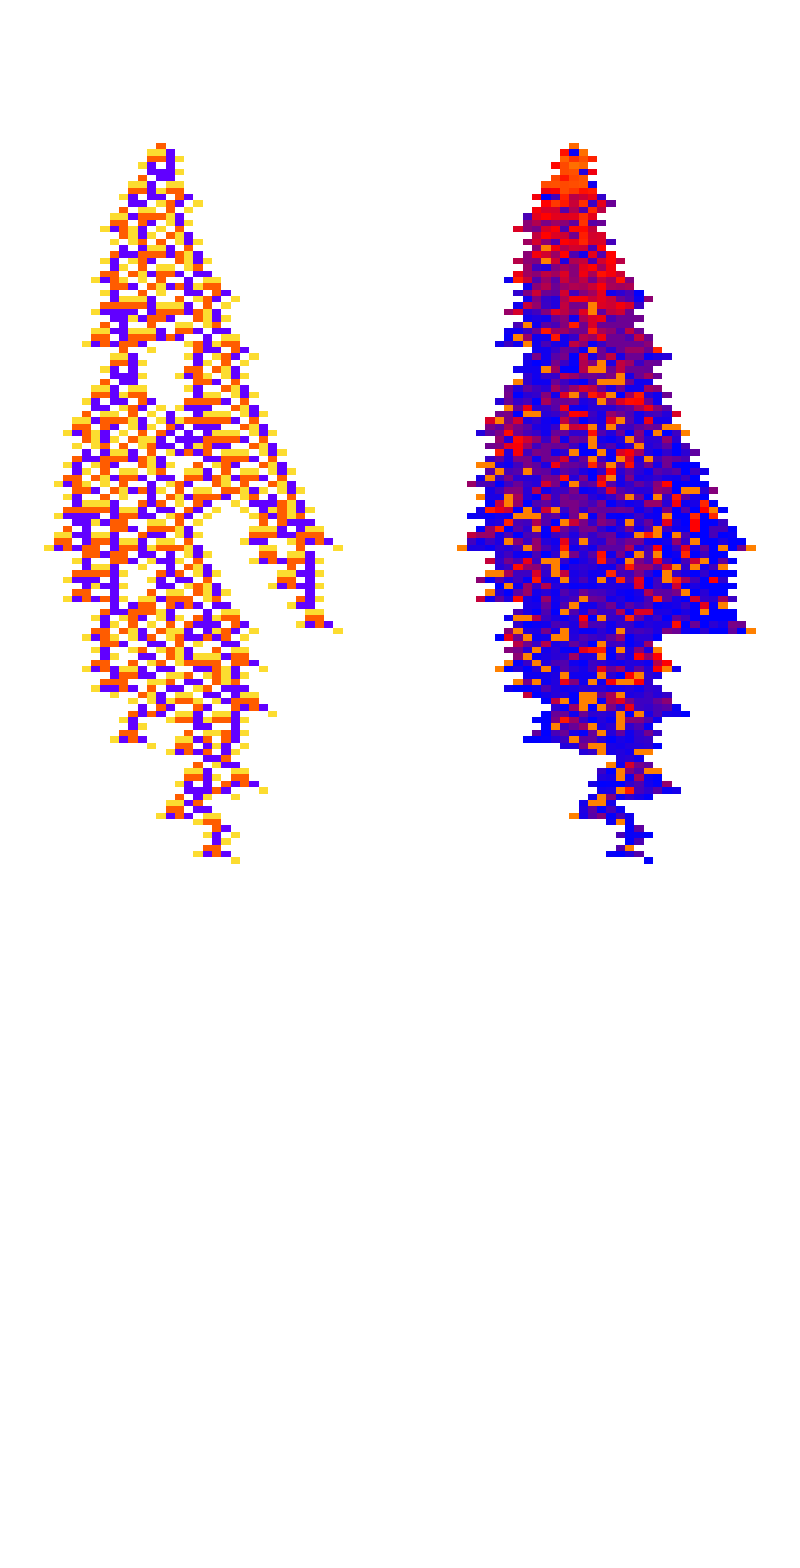

```mathematica
GraphicsRow@({PlotCA[getca[#[[1]], 200]], PerturbationSensitivityPlot[{ getca[#[[1]], 200],#[[1]]}]}&@k4rob[[sirob[[1]]]])
```

Perturbing a section results in similar lifetimes, but all totally different pattens. And there’s no apparent reason why the automata come to an end, they just do:

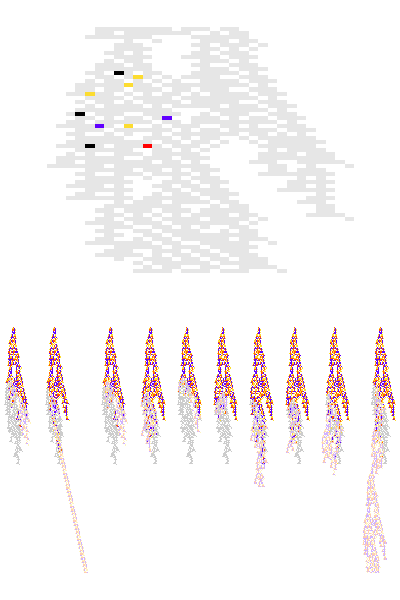

```mathematica
With[{ru =k4rob[[sirob[[1]], 1]],ca = getca[k4rob[[sirob[[1]], 1]] , 200], prus = Table[RandomInteger[{40, 60}]->{RandomSample[Range[1, 10, 1], 1], "Enumerate"}, 10]},
pcasperts = PerturbCA[{ca, ru}, #, "ReturnPerturbations"->True]&/@ prus;
Column@{HighlightPerturbations[ca, Flatten[pcasperts[[All, 2]], 1], "Span"->30;;90, ImageSize->Small],
GraphicsRow[PlotDifferences[ca, #[[1]]]&/@ pcasperts]}]
```

#### Zooming out: Robust vs. Fragile Rules

Looking at all the robustly evolved rules sorted by mean robustness, we can get a sense for the different strategies:

```mathematica
psrob = ParallelMap[PerturbationSensitivityPlot[{ getca[#[[1]], 200],#[[1]]}]&,k4rob[[sirob]]];
```

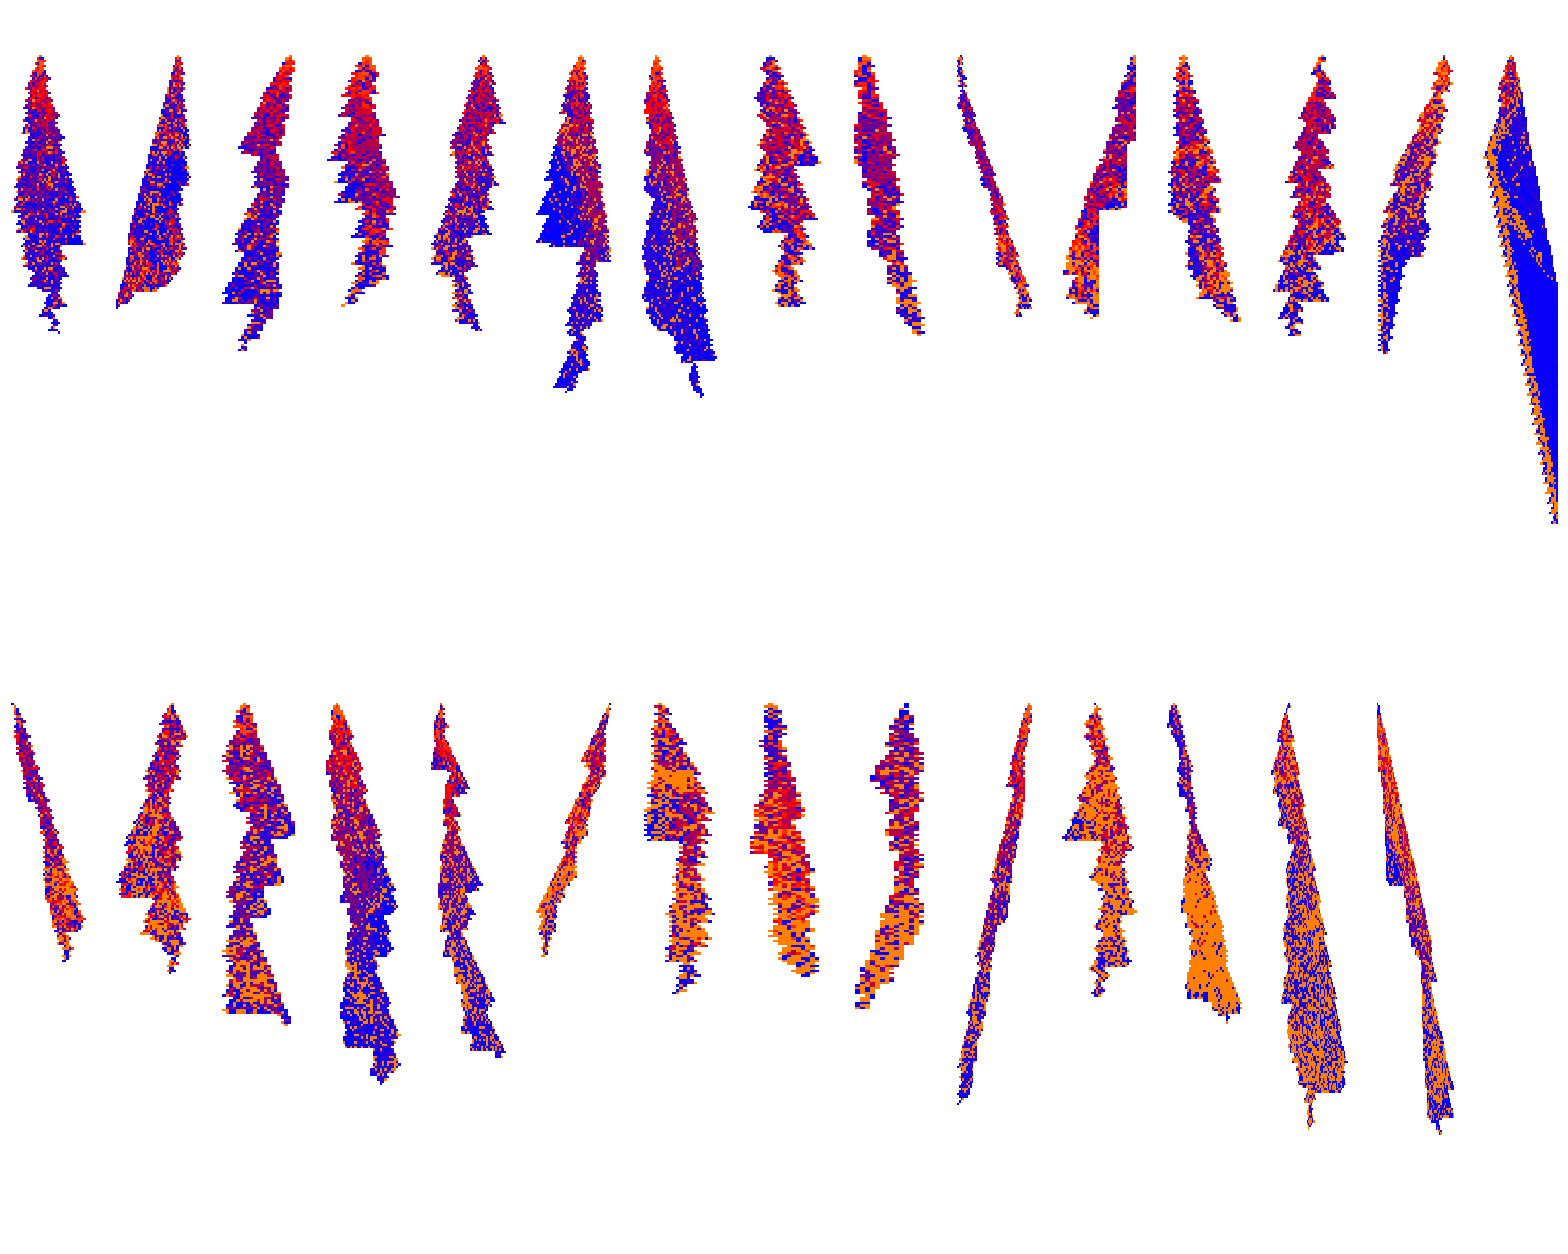

```mathematica
Partition[psrob, 15] // GraphicsGrid
```

And now regular (sorted) for comparison:

```mathematica
psreg = ParallelMap[PerturbationSensitivityPlot[{ getca[#[[1]], 200],#[[1]]}]&,k4reg][[sireg]];
```

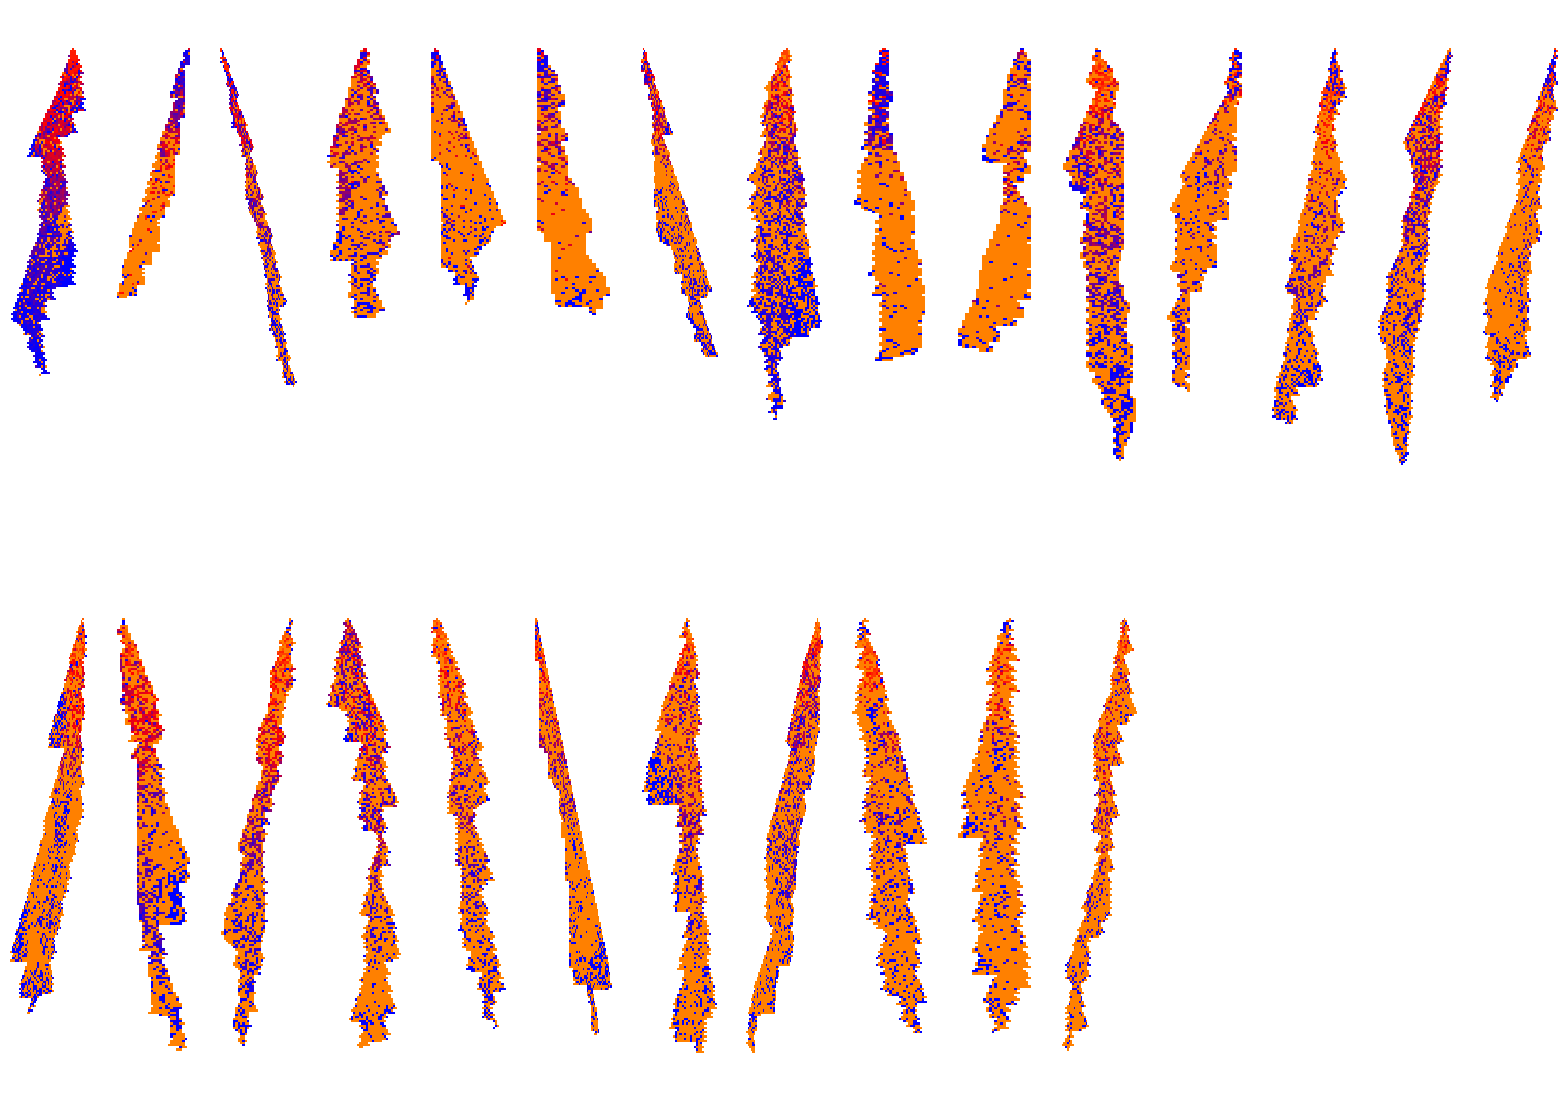

```mathematica
Partition[psreg, 15] // GraphicsGrid
```

So there is a lot going on here. The ones where there are lots of fans out tend to have pockets of robustness near the corners of their fans. And I would say in general early development is more fragile, although not always.

#### Leg skin

Similarly in this rule, the right leg often acts as skin:

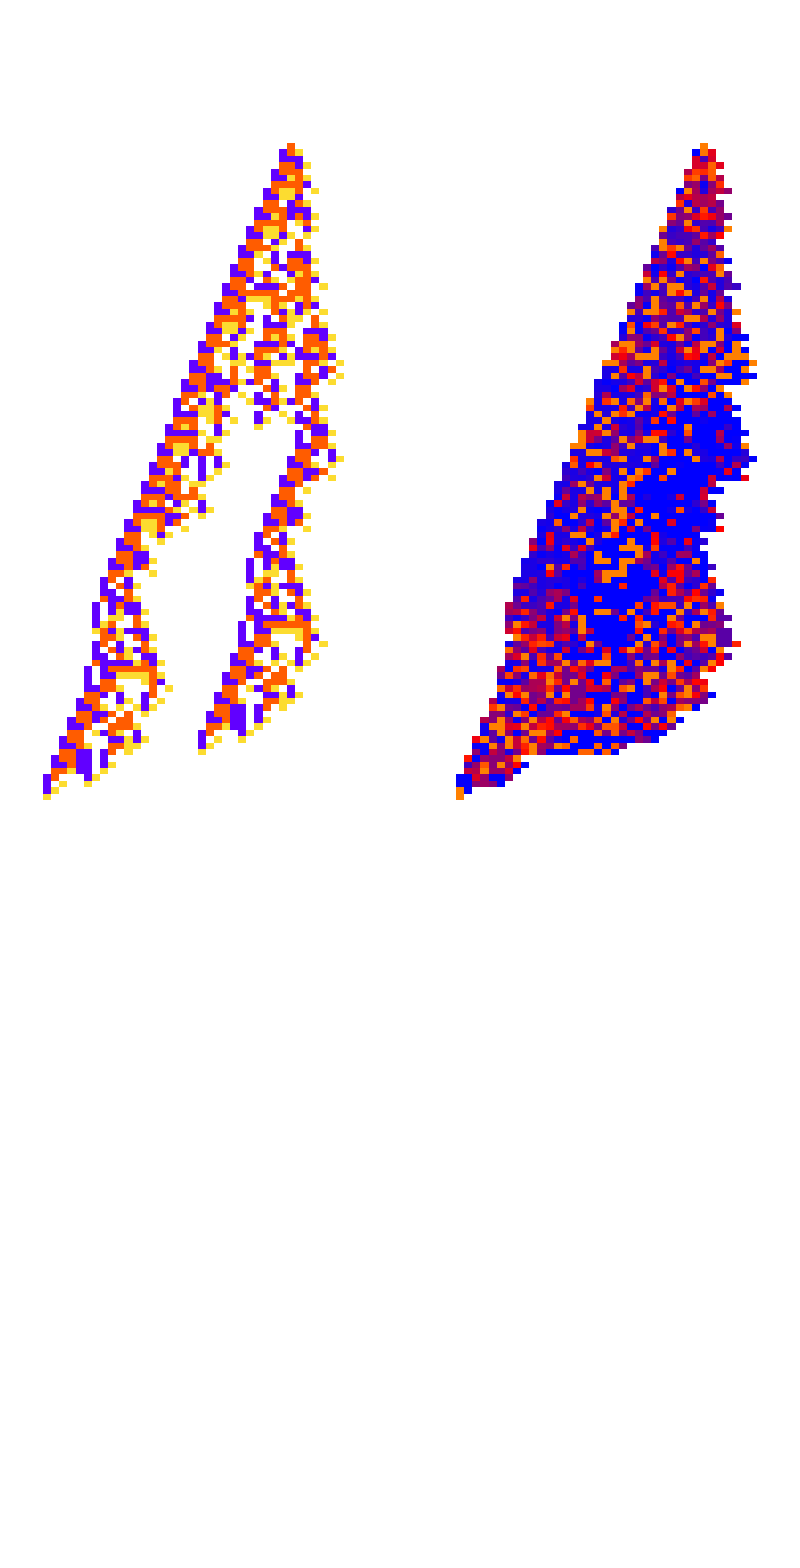

```mathematica
GraphicsRow@({PlotCA[getca[#[[1]], 200]], PerturbationSensitivityPlot[{ getca[#[[1]], 200],#[[1]]}]}&@k4rob[[sirob[[2]]]])
```

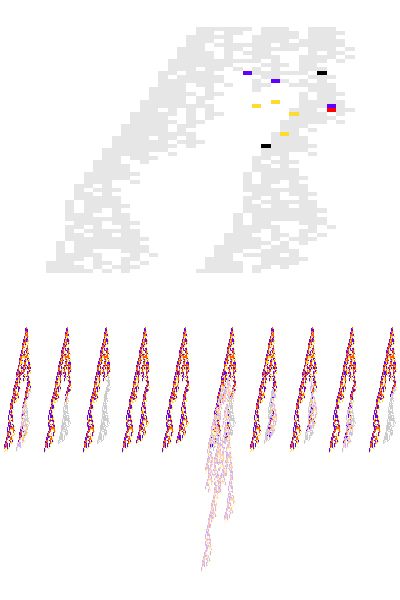

```mathematica
With[{ru =k4rob[[sirob[[2]], 1]],ca = getca[k4rob[[sirob[[2]], 1]] , 200], prus = Table[RandomInteger[{40, 60}]->{RandomSample[-Range[1, 10, 1], 1], "Enumerate"}, 10]},
pcasperts = PerturbCA[{ca, ru}, #, "ReturnPerturbations"->True]&/@ prus;
Column@{HighlightPerturbations[ca, Flatten[pcasperts[[All, 2]], 1], "Span"->30;;90, ImageSize->Small],
GraphicsRow[PlotDifferences[ca, #[[1]]]&/@ pcasperts]}]
```

#### Another “skin” case

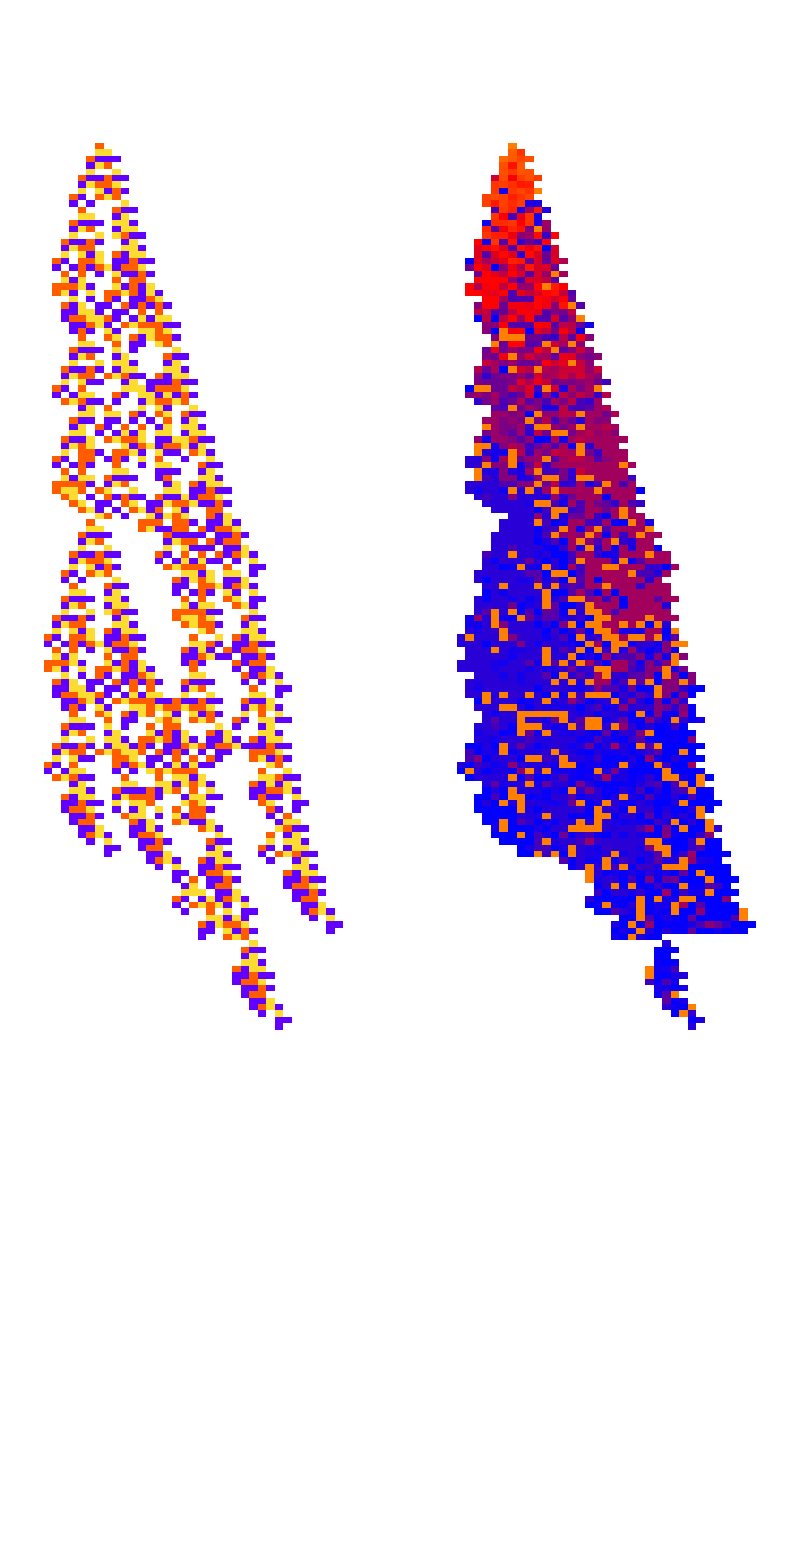

```mathematica
GraphicsRow@({PlotCA[getca[#[[1]], 200]], PerturbationSensitivityPlot[{ getca[#[[1]], 200],#[[1]]}]}&@k4rob[[sirob[[7]]]])
```

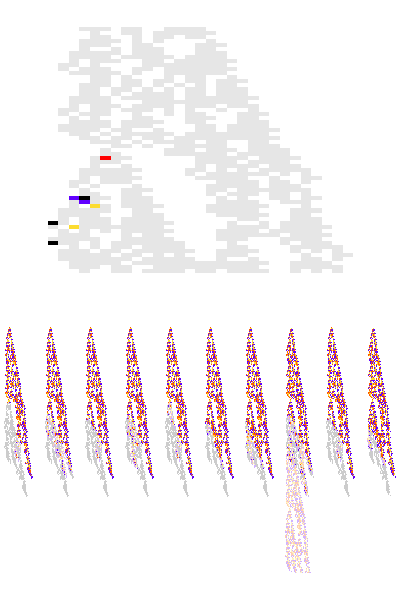

```mathematica
With[{ru =k4rob[[sirob[[7]], 1]],ca = getca[k4rob[[sirob[[7]], 1]] , 200], prus = Table[RandomInteger[{60, 90}]->{RandomSample[Range[1, 3, 1], 1], "Enumerate"}, 10]},
pcasperts = PerturbCA[{ca, ru}, #, "ReturnPerturbations"->True]&/@ prus;
Column@{HighlightPerturbations[ca, Flatten[pcasperts[[All, 2]], 1], "Span"->30;;90, ImageSize->Small],
GraphicsRow[PlotDifferences[ca, #[[1]]]&/@ pcasperts]}]
```

#### More Irreducible Robustness

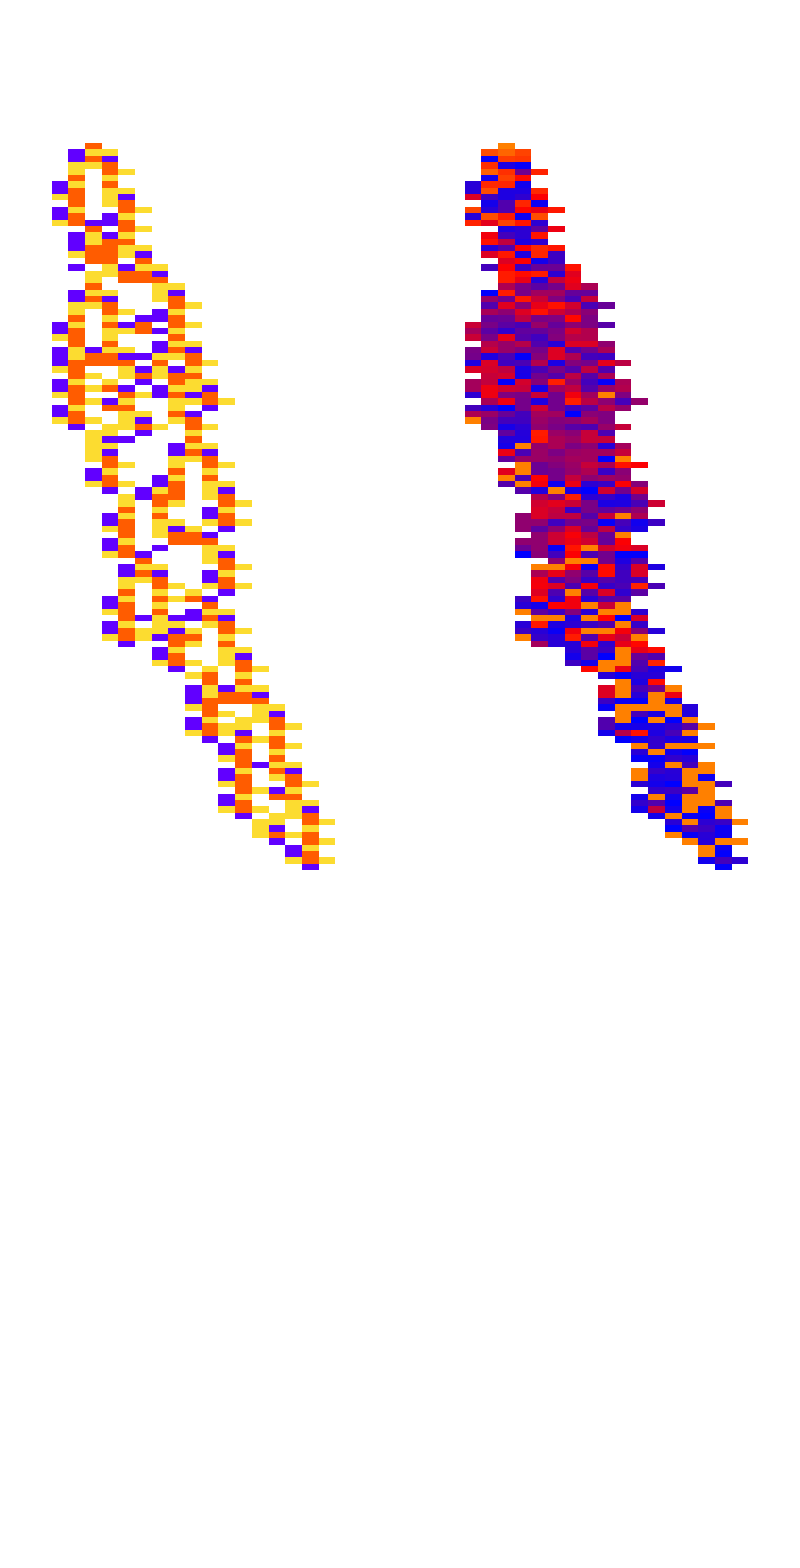

```mathematica
GraphicsRow@({PlotCA[getca[#[[1]], 200]], PerturbationSensitivityPlot[{ getca[#[[1]], 200],#[[1]]}]}&@k4rob[[sirob[[9]]]])
```

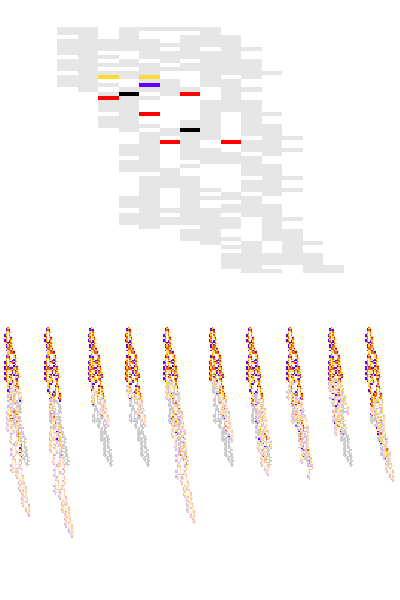

```mathematica
With[{ru =k4rob[[sirob[[9]], 1]],ca = getca[k4rob[[sirob[[9]], 1]] , 200], prus = Table[RandomInteger[{40, 60}]->{RandomSample[Range[1, 5, 1], 1], "Enumerate"}, 10]},
pcasperts = PerturbCA[{ca, ru}, #, "ReturnPerturbations"->True]&/@ prus;
Column@{HighlightPerturbations[ca, Flatten[pcasperts[[All, 2]], 1], "Span"->30;;90, ImageSize->Small],
GraphicsRow[PlotDifferences[ca, #[[1]]]&/@ pcasperts]}]
```

### Trimmed Sensitivity Plot

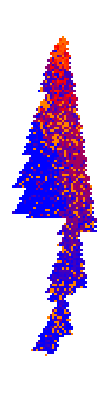

```mathematica
PerturbationSensitivityPlot[{getca[#[[1]], 200],#[[1]]},absdeltalt,"Random", "Trim"->{1,3}]&@k4rob[[sirob[[6]]]]
```

### Propagation of Diseased Tissue

To get an even better sense for the different types of robustness we’re seeing, we can look at the number of different cells at each step after a perturbation. In this case we perturb at step thirty, with the red line corresponding to the original lifetime. And this is a cancerous perturbation so the number of different cells jumps up and then never comes down, eventually giving us a periodic pattern.

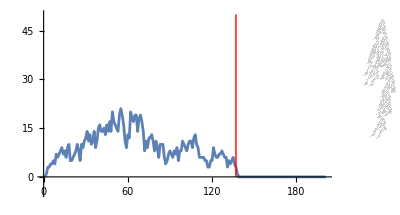

```mathematica
Module[{ru = k4rob[[sirob[[6]], 1]], ca, pcasperts},
 ca = getca[ru];pcasperts = Table[PerturbCA[{ca, ru}, "Random"->1, "ReturnPerturbations"->True],1];
GraphicsRow@{DiseasePropogationPlot[ca, pcasperts], PlotDifferences[ca, pcasperts[[1, 1]]]}]
```

When the perturbation immediately terminates the CA we get something like this, where the differences drop to zero as soon as the lifetime is reached because it is all white for both the perturbed and the regular:

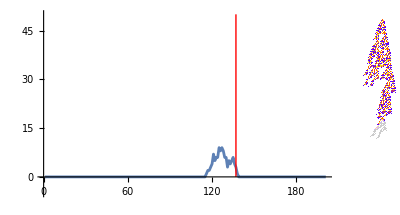

```mathematica
Module[{ru = k4rob[[sirob[[6]], 1]], ca, pcasperts},
 ca = getca[ru];pcasperts = Table[PerturbCA[{ca, ru}, "Random"->1, "ReturnPerturbations"->True],1];
GraphicsRow@{DiseasePropogationPlot[ca, pcasperts], PlotDifferences[ca, pcasperts[[1, 1]]]}]
```

If the perturbation causes a different pattern that still ends up dying out, it looks like this:

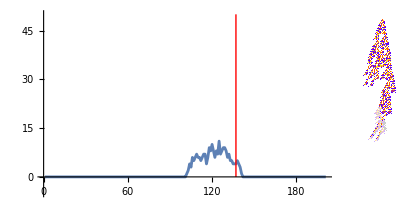

```mathematica
Module[{ru = k4rob[[sirob[[6]], 1]], ca, pcasperts},
 ca = getca[ru];pcasperts = Table[PerturbCA[{ca, ru}, "Random"->1, "ReturnPerturbations"->True],1];
GraphicsRow@{DiseasePropogationPlot[ca, pcasperts], PlotDifferences[ca, pcasperts[[1, 1]]]}]
```

Doing multiple perturbations we can get a sense for how disease propagates from different areas, here we perturb from the 10th step:

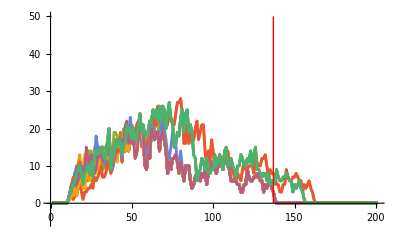

```mathematica
Module[{ru = k4rob[[sirob[[6]], 1]], ca, pcasperts},
 ca = getca[ru];pcasperts = Table[PerturbCA[{ca, ru}, 10->1, "ReturnPerturbations"->True],30];
DiseasePropogationPlot[ca, pcasperts]]
```

Perturbing where this automata has protective tissue we get:

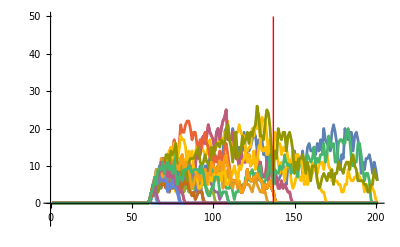

```mathematica
Module[{ru = k4rob[[sirob[[6]], 1]], ca, pcasperts},
 ca = getca[ru];pcasperts = Table[PerturbCA[{ca, ru}, 60->1, "ReturnPerturbations"->True],30];
DiseasePropogationPlot[ca, pcasperts]]
```

So we can see that the propagation of diseased tissue in some cases is stopped, which corresponds to something like getting a cut which then heals over. An even better example of this is big yellow:

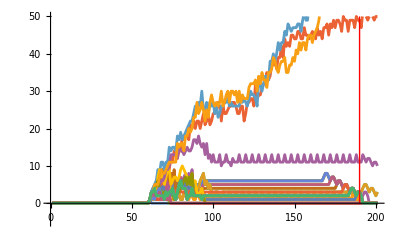

```mathematica
Module[{ru = k4rob[[sirob[[15]], 1]], ca, pcasperts},
 ca = getca[ru];pcasperts = Table[PerturbCA[{ca, ru}, 60->1, "ReturnPerturbations"->True],30];
DiseasePropogationPlot[ca, pcasperts]]
```

Here we can see many cases where the scratch is healed. Looking at perturbations to different lifetimes for big yellow we get:

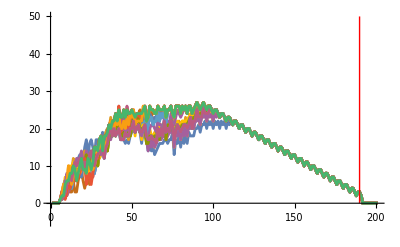
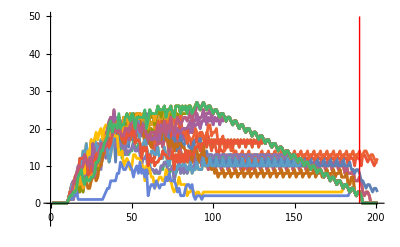
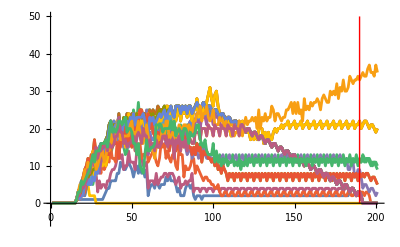
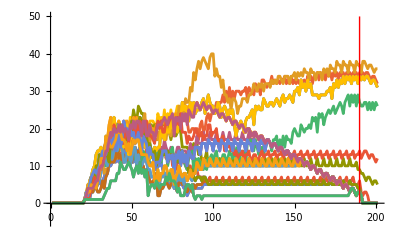
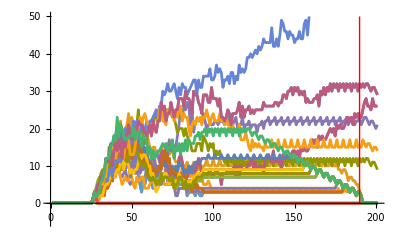
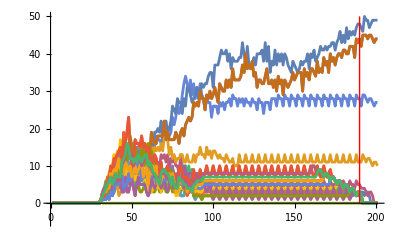
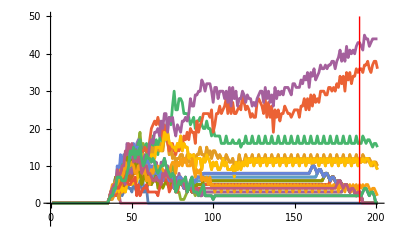
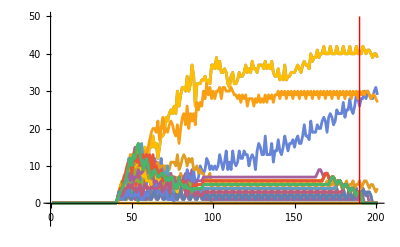
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[DiseasePropogationPlot[k4rob[[sirob[[15]], 1]], i], {i, 5, 90, 5}]
```

So the early perturbations that effect the “essential organs” tend to be more lethal. For comparison here is a the disease propagation for a regularly evolved automata:

```mathematica
Table[DiseasePropogationPlot[k4reg[[1, 1]], i], {i, 5, 90, 5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

So very different from big yellow. And there very few cases of self-healing. But many of the robust rules don’t look like big yellow at all. Here is the irreducibly robust one we were looking at before:

```mathematica
Module[{ru = k4rob[[sirob[[1]], 1]], ca, pcasperts},
 ca = getca[ru];pcasperts = Table[PerturbCA[{ca, ru},50->1, "ReturnPerturbations"->True],30];
GraphicsRow@{DiseasePropogationPlot[ca, pcasperts], PlotDifferences[ca, pcasperts[[1, 1]]]}]
```

-Graphics-

So this one the diseased tissue is just also really good at dying out, and it’s not easy to see why. Looking at different lifetimes:

```mathematica
Table[DiseasePropogationPlot[k4rob[[sirob[[1]], 1]], i], {i, 5, 90, 5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Interestingly, this one also favors later perturbations with step ninety being remarkably unshakeable. And a lot of its advantage is in it’s shorter lifetime because it gives it time to die out. Looking at sample perturbations for all the robustly evolved (sorted by robustness) we get:

```mathematica
Table[DiseasePropogationPlot[k4rob[[sirob[[i]], 1]]],{i, Length[k4rob]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

And all the regular for comparison:

```mathematica
Table[DiseasePropogationPlot[k4reg[[sireg[[i]], 1]]],{i, Length[k4reg]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

One takeaway here is that many of the automata are utilizing irreducible robustness. Meaning, almost all the perturbations cause large differences within a few steps, but those new patterns tend to also die out, as you can see by the frequent return to zero in many automata. Which makes one wonder if it is even possible for these automata to evolve instant healing. Because clearly that is not what they are doing. To get at this we can look at what I’m calling micro fragility graphs.

#### Overlayed Regular vs. Robust Propogation

```mathematica
Table[
(*{PlotCA[k4rob[[sirob[[6]], 1]]], PlotCA[k4reg[[idx, 1]]]}*)
Show[DiseasePropogationPlot[k4rob[[sirob[[6]], 1]], 60,10, PlotStyle->Lighter@Blue], 
DiseasePropogationPlot[k4reg[[idx, 1]], 60,10, PlotStyle->Lighter@Orange]
], {idx, 1, Length[k4reg]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Microfragility

So to get at the possibility of instant-healing, we can look at each potential sequence that can be perturbed. Some sequences tend to be far more frequent, so we show them to scale of their frequency. Then, each edge represents a perturbation, with the color being the number of different cells that that perturbation immediately produces. In this case, red is 3, orange is 2, light green is 1, and solid green is 0. This is a robust rule and the lack of green we see makes sense because we saw that it wasn’t using instant-healing.

```mathematica
Module[{ru = k4rob[[sirob[[2]], 1]], ca},ca = getca[ru];
PerturbationSensitivityGraphs[{ca, ru}, 0.75]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |

We can show this in a more practical (but more boring) bar-chart:

```mathematica
Module[{ru = k4rob[[sirob[[2]], 1]], ca},ca = getca[ru];
PerturbationSensitivityChart[{ca, ru}, "ShowSequences"->True]]
```

-Graphics-

For comparison here is the graph and chart of a regular rule:

```mathematica
Module[{ru = k4reg[[1, 1]], ca},ca = getca[ru];
PerturbationSensitivityGraphs[{ca, ru},0.5]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Module[{ru = k4reg[[1, 1]], ca},ca = getca[ru];
PerturbationSensitivityChart[{ca, ru}, "ShowSequences"->True]
]
```

-Graphics-

All the robust charts:

```mathematica
PerturbationSensitivityChart[{getca[#[[1]]], #[[1]]}]&/@ k4rob[[sirob]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

And all the regular:

```mathematica
PerturbationSensitivityChart[{getca[#[[1]]], #[[1]]}]&/@ k4reg[[sireg]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

So pretty much just a whole lot of orange. And there is no apparent difference between the robust and the regular. But there are many cases where a sequence that is used a lot when perturbed goes to a sequence that is almost never used. In that case, it seems like it would make sense to have the less frequent rule match the more frequent rule, acting as a backup. In other words, to turn the big red edges green. So is this possible?

TODO: Answer this

### Thorough Visualization of Perturbed Evolution

```mathematica
evo = Module[
{steps=4000,maxlen=200, ru, lt, pcas,ca, fitness, lts},
SeedRandom[426788];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
lt=TestCALifeTime[ca = getca[ru, maxlen]];
If[lt == -Infinity, #,
{pcas, perts} = Transpose[Table[PerturbCA[{ca, ru}, RandomInteger[{1, lt}]->1, "ReturnPerturbations"->True], 5]];
fitness = Min[lts = Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Min[Last[#]],{ru,perts, Join[{ca}, pcas], lts},#]
]
]&,{ {0,4,1},{}, {getca[{0,4, 1}, maxlen]},Table[1, 6]},steps]];
```

```mathematica
gevo = GatherBy[evo, Min[#[[4]]]&];
```

```mathematica
PlotCAs/@gevo[[All, 1, 3]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsRow[HighlightPerturbations[#[[1, 3, 1]], Flatten[#[[1, 2]], 1]]&/@ gevo]
```

-Graphics-

Side by side view of perturbations and effects

```mathematica
GraphicsRow/@Transpose[{HighlightPerturbations[#[[1, 3, 1]], Flatten[#[[1, 2]], 1], ColorRules->Join[# -> GrayLevel[0.9] & /@{1,2, 3},
    -#1 -> Red& /@ {-100, 1, 2, 3}]]&/@ gevo, PlotCAs[#[[1, 3]]]&/@gevo}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

All selected perturbed ca lifetimes

```mathematica
ListLinePlot[Transpose@evo[[All, 4]]]
```

-Graphics-

### Thorough history of big yellow

```mathematica
evo3 = Module[{ru, ca, lt, pcas,lts,  fitness},
SeedRandom[426778+132];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
{pcas, perts} = Transpose[Table[PerturbCA[{ca, ru}, RandomInteger[{1, lt}]->1, "ReturnPerturbations"->True], 5]];
fitness = Min[lts = Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Min[Last[#]],{ru,perts, Join[{ca}, pcas], lts},#]
]]&,{{0,4,1},{}, {getca[{0, 4, 1}, 200]}, {0}},2000]
];
```

```mathematica
gevo3 = GatherBy[evo3, Min[#[[4]]]&];
```

```mathematica
gevo3[[9, 1, 1]]
```

{297413941736399379873447198801621939512,4,1}

```mathematica
GraphicsRow[PlotCA/@ gevo3[[All, 1, 1]]]
```

-Graphics-

```mathematica
PlotCAs/@gevo3[[All, 1, 3]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsRow[HighlightPerturbations[#[[1, 3, 1]], Flatten[#[[1, 2]], 1]]&/@ gevo3]
```

-Graphics-

### The Effect of Increasing Perturbation Intensity

Even the robust rules tend to struggle with multiple perturbations. It’s essentially saying what happens if we perturb diseased tissue? It would be interesting to see automata evolved under multi-row perturbations:

```mathematica
bca = getca[bru = k4rob[[sirob[[1]], 1]]];
{pca, perts} = PerturbCA[{bca, bru},NRandomPerts[3, bca], "ReturnPerturbations"->True];
perts;
GraphicsRow[{HighlightPerturbations[pca, perts, ImageSize->Large], PlotDifferences[bca, pca, ImageSize->Large]}]
```

-Graphics-

At three the robustness is dwindling:

```mathematica
GraphicsRow[PlotCA/@ Table[PerturbCA[{bca, bru}, NRandomPerts[3, bca]], 10]]
```

-Graphics-

Interestingly, if you perturb it more times it results in less cancer, because it’s almost like you’re also killing the cancer which is interesting:

```mathematica
GraphicsRow[PlotCA/@ Table[PerturbCA[{bca, bru}, NRandomPerts[10, bca]], 10]]
```

-Graphics-

Now we do it for all the robust rules with perturbation intensity on the x-axis and new lifetime on the y-axis. We replace -Infinity with zero and we see that in all rules, there is a loss of robustness with higher disease intensity, which makes sense. The way in which the different automata react varies greatly though, some are immediately mangled by three perturbations, while others can deal with some higher intensity. Some slowly move towards fragility while others have a sudden “phase-transition”.

```mathematica
ParallelTable[Module[{ru  =k4rob[[sirob[[k]], 1]], ca, lt},
ca = getca[ru];lt = TestCALifeTime[ca];
DistributionChart[Table[Table[TestCALifeTime[PerturbCA[{ca, ru}, NRandomPerts[i, lt]]], 100]/.-Infinity->0, {i, 1, 10}]]], {k, 1, Length[k4rob]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Can you get stuck? k = 4 multiway rule graph

Starting from a “stuck” rule looking at all possible rules one step away we can see that none of them are larger than 1 or infinity

```mathematica
NestGraph[getallmutations,{{287096442033201941006168304425662446752,4,1}},1,VertexShapeFunction->(Inset[TestLifetime[#2,200],#1]&), VertexStyle->Black]
```

-Graphics-

Looking at two steps, there are too many rules to see the graph but we see that none of them are larger than 1 or equal to -Infinity

```mathematica
ng = NestGraph[getallmutations,{{287096442033201941006168304425662446752,4,1}},2]
```

```mathematica
lts = TestLifetime/@VertexList@ng
```

```mathematica
{Length[lts],
Count[lts, lt_/;lt == 1 || lt == -Infinity]}
```

{17767,17767}

Going more than two steps is very computationally expensive but in an evolution they’re really just trying to trace a never-go-down path, so we can look at a sample path

```mathematica
tried = {};
evo=Module[{ru, life},NestList[CompoundExpression[
 ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,100],
AppendTo[tried,{ru, life}],
If[life>=Last[#],{ru,life},#]
]&,{{287096442033201941006168304425662446752,4,1},0},1000]];
```

And it can’t get unstuck:

```mathematica
ListLinePlot[tried[[All, 2]], PlotHighlighting->None]
```

-Graphics-

```mathematica
tried[[All, 1]]
```

{{287096440765551340777938902928959241376,4,1},{287096440765551340787162274965814017184,4,1},{287096440765551340787162279363860528288,4,1},{287096440607095015758633604176772627616,4,1},{287097414162755991038813953644834356384,4,1},{287097414162755991038813953713553833120,4,1},{287097414162755991038813953713554095264,4,1},{287097353315527180083802681871800237216,4,1},{286432739317634722147350778341660064928,4,1},{286432739317634722147350778341657967776,4,1},{286432739317634720966759157624246664352,4,1},{286432739317634872082486609452893502624,4,1},{286437931614493406910115139949222722720,4,1},{286437931614493406614967234769869896864,4,1},{286437951896903010266637658717121182880,4,1},{286437931614493406614967234769869896864,4,1},{286437931614493416059700200509160324256,4,1},{286437931614493416059699074609253481632,4,1},{286437931614493416059699074677972958368,4,1},{286437931619445176216840595777569455264,4,1},{286437931619445195106306527256150310048,4,1},{286437932570183145277478578378677714080,4,1},{307705580502741799243939491343163227296,4,1},{307705580502741799243939491343163227232,4,1},{307705580502741799243940617243070069856,4,1},{307705580502741799243940617243204287584,4,1},{307705580502741799243940617243204287520,4,1},{307705579868916499129825916494852684832,4,1},{307705579868916480240359985016271830048,4,1},{265170284003799172307438159087300803616,4,1},{265170284003953914812348831621663194144,4,1},{265170284023760955440914916020049181728,4,1},{265170284023760955440913790120142339104,4,1},{265170284024070440450735135188867120160,4,1},{265170284024080111857292052222264769568,4,1},{265170284024099454670405886289060068384,4,1},{265170284024099454670407012188966911008,4,1},{265170284024099454661183640152112135200,4,1},{265170284043906495289749724550498122784,4,1},{265170284043906495289767738949007604768,4,1},{265170278973304094376850132962194783264,4,1},{265170278973303187682485421990313753632,4,1},{286437926905861841648946334954799266848,4,1},{286437926905629727891580326153255681056,4,1},{286437926905629727891580326428133588000,4,1},{286437926905629727891580326428133588256,4,1},{286437926905629726710988705710722284576,4,1},{286436628831415093004081573086639979552,4,1},{286436628831415093004081568688593468448,4,1},{286436628831415093004009511094555540512,4,1},{31224853640711245406478555520729381920,4,1},{31204084453277106095964433535412501536,4,1},{31204084453431848600875106069774892064,4,1},{31204084453431848600875106069758114848,4,1},{31204084453431848600875106069766503456,4,1},{31204084453393162974647437936175905824,4,1},{30871777454446934006421486171105819680,4,1},{30871777454446934006421487270617447456,4,1},{30871777454446934006421487270617443360,4,1},{30871777454446934301569392449970269216,4,1},{30871777454446934301569392449836051488,4,1},{30871777454446934301569392449836048416,4,1},{30871777454446934301569251712347693088,4,1},{30871777451971054222998491162549444640,4,1},{30871777451971054222998491025110491168,4,1},{30871777453208994262283871300009615392,4,1},{30871777453054251757373198765647224864,4,1},{30871777453054251757373198765638836256,4,1},{30871777453054251757373198766175707168,4,1},{30871777453054252347669009124881358880,4,1},{30871777453054252347669009124882407456,4,1},{30871777453054252347669009124880310304,4,1},{30871777453054252347668727649903599648,4,1},{30871777453073595160782561716698898464,4,1},{30871128415966278307328995404657745952,4,1},{30871128415966278307333499004285116448,4,1},{30871128415927592681105830870694518816,4,1},{30871128415927592681105813278508474400,4,1},{30871133486529993594023419265321295904,4,1},{30871128415927592681105813278508474400,4,1},{30871128415927592681105813278642692128,4,1},{30829590041059314060077569308008931360,4,1},{30829590041059314060077604492381020192,4,1},{30829591308709914288307005989084225568,4,1},{30829591308710518751216813303671578656,4,1},{30829591308710518751216813320851447840,4,1},{30829591308710518714323325173432344608,4,1},{30829591308710518566749372583755931680,4,1},{30829591307782063537285337377581588512,4,1},{30829591307782063537285337377581572128,4,1},{30829591307782063537285337377044701216,4,1},{30829591309020003576570717651943825440,4,1},{30829591309039346389684551718739124256,4,1},{30829591309039348750867793153561731104,4,1},{25512679325899685259252564912440352800,4,1},{25512679325899685259252564912373243936,4,1},{25512679325899686439844185629784547360,4,1},{21524995338544938821132764448943513632,4,1},{21525319857098597247859547604964089888,4,1},{22854547852883513120763354665244434464,4,1},{22854547852883513120763354665248628768,4,1},{192995731313352744852450658381132734496,4,1},{192995731313372087665564492447928033312,4,1},{192996055831925746092291275603948609568,4,1},{192996055831925746092291275672668086304,4,1},{192996055831945088905405109739463385120,4,1},{192996055831945088942298597886882488352,4,1},{192996055832564058961941288024332050464,4,1},{192996055832564058961941270432146006048,4,1},{192996055832564058961939018632332320800,4,1},{214263703765122712928399931596817834016,4,1},{214263703765123015159854835254111510560,4,1},{214263703755219494845571793054918516768,4,1},{214014473506009823119402329231115952160,4,1},{214014534353238634074413601072869810208,4,1},{214014534353238634073837140320566386720,4,1},{214014534353238634073837149116659408928,4,1},{214014534353238634073837149116659409056,4,1},{214014534353238634073837149047939932320,4,1},{214014534353199948447609480914349334688,4,1},{214014534358151708604751002013945831584,4,1},{214014533090501108376521600517242626208,4,1},{214014533090501108376521582925056581792,4,1},{214014533090501108376521583199934488736,4,1},{214014533090501108376521583208524423328,4,1},{214014533090501108376521583337373442208,4,1},{214014533090501108376521583337373491360,4,1},{214014533090501108376521583337373474976,4,1},{214014533090501108376526086937000845472,4,1},{214014543231705910202361298910626488480,4,1},{214014543231705910202361580385603199136,4,1},{214679157229598368138813483915743371424,4,1},{214679157229598367843665578736390545568,4,1},{214679162300200768756583184723203367072,4,1},{214677864225986135049676052099121062048,4,1},{214677864859811435163790752847472664736,4,1},{214677864859811439886157235717117878432,4,1},{214677864859811439886157235717654749344,4,1},{214677864859811439886157446823887282336,4,1},{214677864859811439887022137952342417568,4,1},{225311688826090766870252594434585174176,4,1},{225311688826090766870252594434585141408,4,1},{225311688826090766870252594434635473056,4,1},{225312986900305400577159727058717778080,4,1},{225312986905257160734301248158314274976,4,1},{225312986905257160715854504084604723360,4,1},{219996074922117497224239275843483345056,4,1},{219996074922117497224239275841335861408,4,1},{219996074919641617145668515291537612960,4,1},{219996074919641617145668515291537809568,4,1},{219996074919641617145671892991258337440,4,1},{219996074919641617440819798170611163296,4,1},{219996074919641612718453315300965949600,4,1},{219996074919641611833009599762907472032,4,1},{219996074919641611833009599488029565088,4,1},{219996074919641611832937541893991637152,4,1},{219996034354822404529596693999489065120,4,1},{220079111104558961771653181940756586656,4,1},{220079111183787124285917519534300536992,4,1},{220079111183787124285917238059323826336,4,1},{220079111183787124285989295653361754272,4,1},{220079354572702368106034383020377186464,4,1},{220079354572702368106034383033262088352,4,1},{220079354572702368069140894872958083232,4,1},{220079355840352968297370296369661288608,4,1},{220076759691923700883556031121496678560,4,1},{220076759691904358070442197054701379744,4,1},{220076759691904358070441985948468846752,4,1},{220076759691904358070441985947931975840,4,1},{220076759692059100575352658482294366368,4,1},{220076759692059100575352658447934628000,4,1},{220076759692059100575352658447934628004,4,1},{220076759692059100575352658447934627984,4,1},{220076759692059100574199736943327781008,4,1},{220076759692059100574199736943327781012,4,1},{220076759692059100574199736960507650192,4,1},{220076759692059100574199736960507650200,4,1},{220242913191532215058312712843042693264,4,1},{220242913191532205613579747103752265872,4,1},{220242913191532205613579738307659243664,4,1},{220242913191532205613579738307608912016,4,1},{220242913191532205615885581316822605968,4,1},{220242913191532205763459533906499018896,4,1},{305313504921766821629303185764441071760,4,1},{305313494780562019803467973790815428752,4,1},{305313494780562019803467973795110396048,4,1},{305313494780562019803467973790815432848,4,1},{305313494783037899882038734340613681296,4,1},{305313494783037899878579969826793140368,4,1},{303984266787252984005676162766512795792,4,1},{303984266767445943377110078368126808208,4,1},{303984266767445943377110641318080229520,4,1},{303984266767755428386931986386805010576,4,1},{303984266926211753415460661573892911248,4,1},{303651959927265524447234709808822825104,4,1},{304316573925157982383686613338962997392,4,1},{314950397891437309366917069821205754000,4,1},{314954292114081210487638467693452669072,4,1},{314954292114081210524531955840871772304,4,1},{314954292114071539117975038807474122896,4,1},{314954292114072748043794653436648829072,4,1},{314954292114072748043794653436648829840,4,1},{314954292114072748043794653436581720208,4,1},{314954312396482351695465077383833006224,4,1},{314954312396172866685643732315108225168,4,1},{314959504693031401513272262811437445264,4,1},{314876427943294844271215774870169923728,4,1},{314876427943292426419576545611820511376,4,1},{314876427943292407530110614133239656592,4,1},{314876427943292407530109488233332813968,4,1},{314876427943292407530109490432356069520,4,1},{314876427943292407530109560801100247184,4,1},{314876427943292407534721246819527635088,4,1},{314876427943292407534721246818453893264,4,1},{314876184554377163714676159451438461072,4,1},{314876184554377163716982002460652155024,4,1},{314881376851235698544610532956981375120,4,1},{314881376851235698544610532956985569424,4,1},{314881376851235698563057277030695121040,4,1},{314881376851235698562913161842619265168,4,1},{314881376847521878445057021017921892496,4,1},{314877482624877977324335623145674977424,4,1},{314877482624877977324333371345861292176,4,1},{314877482624877977324333371358746194064,4,1},{314877563754516391931015067134866436240,4,1},{314877563754516391930979038337847472272,4,1},{304243739788237064947748581855604715664,4,1},{304243739788237064947460351479453003920,4,1},{304243739788237079114559800088388645008,4,1},{304246335936666346528374065336553255056,4,1},{304246335936666346528374065338700738704,4,1},{304246335698981858985581052558068887696,4,1},{304246335698981859575876862916774539408,4,1},{304246335698981850131143897177484112016,4,1},{306904791690551681876951511298044801168,4,1},{306904791690551681876951507999509917840,4,1},{306904791690551681881563194017937305744,4,1},{306904791690551681881563194018004414608,4,1},{306904791690551681879257351008790720656,4,1},{306904791690551681879257351008790716560,4,1},{306904791690551681657896422124276097168,4,1},{306904791690551681657896422128571064464,4,1},{306904791690551681660202265133489791120,4,1},{306904791690551681807776217723166204048,4,1},{306904791690861166817597562791890985104,4,1},{306904796761463567730515168778703806608,4,1},{306904796761463567730515168778703806624,4,1},{306904796762701507769800549053602930848,4,1},{306904796762701512492167031923248144544,4,1},{328172444695260166458627944887733657760,4,1},{328172444061434866344513244139382055072,4,1},{328172444081241906973079328537768042656,4,1},{328172444081241906973079610012744753312,4,1},{328172444081241906973079610017039720608,4,1},{328172444081241906973079610012744756384,4,1},{328162059487524837317822549020086316192,4,1},{328162059487524232854912741705498963104,4,1},{328162059487524232928699718000337169568,4,1},{328162059486286292889414337725438045344,4,1},{328162059486286292889414337726511787168,4,1},{328172444080003362544671398719170227360,4,1},{328255520829739919786727886660437748896,4,1},{328255520829739919786727886660437744800,4,1},{328255520829739919786727886660437220512,4,1},{327258599832901232882050031365226962080,4,1},{327258599832901232882050031348047092896,4,1},{327258599832901232882050031399586700448,4,1},{327253407536042698054421500903257480352,4,1},{327004177286833026328252037079454915744,4,1},{327004177286833026328252037079458061472,4,1},{327004177286833026328238526280575949984,4,1},{327170330786306140812351502163110993056,4,1},{321853418803166477320736273921989614752,4,1},{321853418803166477321889195426596461728,4,1},{321853418803166477321889195409416592544,4,1},{321853418803166472599522712539771378848,4,1},{321853418803166472599522712539771428000,4,1},{321853418803166472599522712539771231392,4,1},{258050475005490510700139973646314691744,4,1},{258050475005490510700139973646365023392,4,1},{258050475005181025690318628577640242336,4,1},{258050495287590629341989052524891528352,4,1},{258050475005181025690318628577640242336,4,1},{258050475005181025690318628577774460064,4,1},{258050475005181022148543766425540549792,4,1},{258050475005181022148579795222559513760,4,1},{258050475005181024509763036657382120608,4,1},{258050475005181024509763036657381072032,4,1},{258050475005181024509763036623021333664,4,1},{259379703000965940382666843683301678240,4,1},{259379703000965940382666843683301678752,4,1},{259379703000985283195780677750096977056,4,1},{259379703000986492121600292379271683232,4,1},{259379703000986492112376920342416907424,4,1},{259379703000986492112088689966265195680,4,1},{259379703000986492112088689964117712032,4,1},{260376623997825179016766545259327970464,4,1},{260210470498352064532653569376792927392,4,1},{260210470498352064541876941413647703200,4,1},{260210470498352064468089965118809496736,4,1},{260210389368713649861408269329804352672,4,1},{260210389368713649861984730082107776160,4,1},{258881161372928733989080923021827431584,4,1},{258881161372928733989080923021827431588,4,1},{258881161372928733989080923021823237280,4,1},{258881161372929338451990730336410590368,4,1},{258881161372929338451990730336410594464,4,1},{258881161372939009858547647369808243872,4,1},{258881161372939009858547647369806146720,4,1},{258881161372939014580914130239451360416,4,1},{258882459447153648287821262863533665440,4,1},{258882459447153648287821262863533927584,4,1},{258882459447153648287820981388557216928,4,1},{258882459447153649468412602105968520352,4,1},{258882459447153649468412602118853422240,4,1},{258882459447153649454577544050686356640,4,1},{258882459447153649454559529652176874656,4,1},{258882459447153649454559529652176866464,4,1},{258882459447153649454559529652176866480,4,1},{258882459447153649454559529652176867248,4,1},{258872074853436579799302468659518426288,4,1},{258872074853436579799302468661665909936,4,1},{258872074536523929742245118287490108592,4,1},{258872074536523929741380427159034973360,4,1},{258872074536523929741380427159034972336,4,1},{258877266833382464569008957655364192432,4,1},{258877266833382464569008953257317681328,4,1},{258877266833382459846642470387672467632,4,1},{258877266833382459846642470387672466608,4,1},{258877266833382535404506196301995885744,4,1},{258877266834620475443791576576895009968,4,1},{258877266834620248770200398833924752560,4,1},{258877266834620248770200680308901463216,4,1},{258877266795006167513068511512129488048,4,1},{258875968720791533806161378888047183024,4,1},{258875968720791533806161378888047182896,4,1},{258875968720791533807026070016502318128,4,1},{258876212109706777627071157383517750320,4,1},{258876213060444727798243208506045154352,4,1},{258876213060444727798243208505994822704,4,1},{258876213060444727794784443992174281776,4,1},{258876213060444727798243208505994822704,4,1},{258876213060444727798243208505994806320,4,1},{258543906061498498830017256740924720176,4,1},{258543906061498498830017256740924720144,4,1},{258543906061498498830017256740924720656,4,1},{258543906061498196598562353083631043600,4,1},{258543906061498196598566856683258414096,4,1},{258543885779088592946896432736007128080,4,1},{258543885779088592799322480146330715152,4,1},{258543642390173348979277392779315282960,4,1},{258543642390173348979313421576334246928,4,1},{258543642390173348979313421593514116112,4,1},{258543642390173348979313421593547670544,4,1},{258543642390173348979313421610727539728,4,1},{258543642390173348979308918011100169232,4,1},{258543642390173348979380975605138097168,4,1},{258543642390173348979380975605138228240,4,1},{258543642390173348978804514852834804752,4,1},{258543642390174557904624129482009510928,4,1},{258543642390174557904624129482009494544,4,1},{258543641122523957676394727985306289168,4,1},{258543640488698657562280027236954686480,4,1},{258543640488698657562280027236820468752,4,1},{258543640488698657562280097605564646416,4,1},{258543640488698657562280097605497537552,4,1},{258543640488698657562280097609792504848,4,1},{258543640488698657571503469642352313360,4,1},{258543640488698657576115155660779701264,4,1},{258543640488389172566293810592054920208,4,1},{258543620205979568914623386644803634192,4,1},{258543620205979568914623388843826889744,4,1},{258543620205979568914623388843893998608,4,1},{258543620205979568914623388843893933072,4,1},{258543620205979871146078292501187609616,4,1},{258543620205979871146078292501187609624,4,1},{258543620205979908925010155458349319184,4,1},{258543620205979908925010155458349319192,4,1},{269177444172259235908240611940592075792,4,1},{269177444172259235908239767515661943824,4,1},{269177444172259232366464905363428033552,4,1},{269174848023829964952650640115263423504,4,1},{269174848023829964949191875601442882576,4,1},{269174848023829964949205386400324994064,4,1},{269174848023829964949205386400325256208,4,1},{269174848023829964949205456769069433872,4,1},{269174848023829964949205439176883389456,4,1},{269174848023829360486295631862296036368,4,1},{269174848023834196189574090378994861072,4,1},{269174848023853539002687924445790159888,4,1},{269174848023853765676279102188760417296,4,1},{269174848023853765676279102188760419344,4,1},{269174848023853765676279102185539193872,4,1},{269178742246497666797000500057786108944,4,1},{269178742246497667018361428942300728336,4,1},{269178742246497662295994946072655514640,4,1},{269178742241545902138853424973059017744,4,1},{269178742241545902138853424973059015696,4,1},{269178742241545902138853424973059016464,4,1},{269178742241545902138853424973059146768,4,1},{269178742241545845470455630537316582416,4,1},{269178742241545845470455630537316582428,4,1},{269178742241545845470455630537316582544,4,1},{269174848018901944349734232665069667472,4,1},{269174848018901944275947256370231461008,4,1},{269175010278178773489310647948241749136,4,1},{269175010278178773489310645749218493584,4,1},{269175010278198116302424479816013792400,4,1},{269175010278198116302424479833193661584,4,1},{269175010278198116302424479841783596176,4,1},{269175010278198116302424479833193399440,4,1},{269175015348800517215342085820006220944,4,1},{269175015348800517215342085819989443728,4,1},{269175015348800517215342085820123661456,4,1},{269175015348800517215342085820123661460,4,1},{269174690830246858788615302664103085200,4,1},{269174690830246858789191763416406508688,4,1},{269174690830246858789191763416409654416,4,1},{269174690831484798828477143691308778640,4,1},{269174680690279997002641931717683135632,4,1},{258540856724000670019411475235440379024,4,1},{258540856724000670000964731161730827408,4,1},{258540856724000670019411475235440379024,4,1},{88399673263531438287724171519556273296,4,1},{130934969128648746220645997448527299728,4,1},{130934969128645119443187153561003181200,4,1},{130976507503513398064215397531636941968,4,1},{130976507503513397769067492352284116112,4,1},{216047099233748013634911144210226168976,4,1},{216047099233748013634911144210259723408,4,1},{216047099233748013634911144213480948880,4,1},{216047099233738342228354227180083299472,4,1},{216047099233738342228354227180083300496,4,1},{216047099233748013634911144213480949904,4,1},{231997835183167004109756828936845084816,4,1},{231997835183167004109756828661967177872,4,1},{231997835183167004109760206361687705744,4,1},{231997835183167004109760206361687706256,4,1},{231997835183167004109760207186321426576,4,1},{231997835183166928551896481271998007440,4,1},{231997186146059611698442914959956854928,4,1},{232007570739776681353699975952615295120,4,1},{232007570739776983585154879609908971664,4,1},{210739922807218329618693966645423458448,4,1},{210739922804742449540123206095625210000,4,1},{210739922804742449540123206026905733264,4,1},{210739921537091849311893804530202527888,4,1},{210739921537091849311893804528055044240,4,1},{210743815759735750432615202400301959312,4,1},{210743815759735750432615202400301960080,4,1},{210743815759735750432615202125424052368,4,1},{210743815759735750432615201850546145424,4,1},{210743815759726079026058284817148496016,4,1},{210743815759726079026022256020129532048,4,1},{210743815759726079026022264816222554256,4,1},{210743815759726079026022264816222554512,4,1},{210743815759726079026022053709990021264,4,1},{212073043755510994898925860770270365840,4,1},{212073043438598344841868510396094564496,4,1},{212073043439836284881153890670993688720,4,1},{208085359452481537262442469490152654992,4,1},{208085359769394187319499819864328456336,4,1},{208085359769394187319499822063351711888,4,1},{186817711836835533353038909098866198672,4,1},{186817711836835533352174217970411063440,4,1},{186817711836835533352174217979000998032,4,1},{186817711837145018361995563039135844496,4,1},{186817711837145018361995554243042822288,4,1},{186817711837145018364301397252256516240,4,1},{186817712154057668421358747626432317584,4,1},{186817712154057668421358747626163882128,4,1},{186817712154057668420205826121557035152,4,1},{186817631024419253813524130332551891088,4,1},{186796861836985114503010008347235010704,4,1},{186796861836907743250554672080053815440,4,1},{186796780707269328643872976291048671376,4,1},{186796780707269328643873117028537026704,4,1},{101726188977034712778029465170594973840,4,1},{101726188977034712630455512580918560912,4,1},{101726188996841753259021596979304548496,4,1},{101726188996841753259021596987894483088,4,1},{101726188996841753259003582580795066512,4,1},{101726188996841753259003582580795064464,4,1},{101726187729191153030774181084091859088,4,1},{101726187729191001915046729255445020816,4,1},{101726187729500486924868074324169801872,4,1},{101726187729500789156322977981463478416,4,1},{101726187729500789156323822406393610384,4,1},{101726268859139203763005518195398754448,4,1},{101726309423958411066346366089901326480,4,1},{101726309422720471027060985815002202256,4,1},{101726309422701128213947151748206903440,4,1},{101726309422701128213946307323276771472,4,1},{101726309422701128213946307323276783760,4,1},{101726309432604648528229349522469777552,4,1},{101726309432604648528229358318562799760,4,1},{101726309432604648749590287203077419152,4,1},{101726309432604648749590287203077435536,4,1},{101726309432604648749590287205224919184,4,1},{101726309432604648749590287203077435536,4,1},{101726309432604648749590287204151177360,4,1},{101726309432604648749590287204151144592,4,1},{101726309432604648749590278408058122384,4,1},{101726309432604648749590278408058123152,4,1},{101726309432604648749590279507569750160,4,1},{101726471691881477962953671085580038288,4,1},{102058778690827706931179622850650124432,4,1},{102058778690827706931179622850650124368,4,1},{102058778690827706931179622850650125136,4,1},{102058778690827706931179622850515906640,4,1},{101726471691881477962953671085445820496,4,1},{101726471691881477962953675483492331600,4,1},{101726471691881477962953675483492331604,4,1},{101721279395022943135325144987163111504,4,1},{101721279395022943135469260175238967376,4,1},{101721279395022943135469260175247355984,4,1},{101721279395022943135469260106527879248,4,1},{101721279395022943135469260106519490640,4,1},{101721238830203735832128412212016918608,4,1},{85770502880784745357282727488652783696,4,1},{85770502880784443125827823831359107152,4,1},{85770502880784443125814313032476995664,4,1},{85770502880784480904746175989638705232,4,1},{85770502880784480890911117934356541520,4,1},{85770502880784480890911117934893412432,4,1},{85770502880784707564502295677863669840,4,1},{85770503118469195107295308458495520848,4,1},{85770502960012870078766633271407620176,4,1},{85770543524832077382107481165910192208,4,1},{85770381265555248168744089587899904080,4,1},{85770705784108906595470872743920480336,4,1},{85770705803915947224036957142306467920,4,1},{85770705170090647109922256393954865232,4,1},{85770705170090647109922256402544799824,4,1},{85770705170090647109922819343908286544,4,1},{85770705170090647109922819343908319312,4,1},{85770380651536988683196036187887743056,4,1},{85767784503107721269381770939723133008,4,1},{85767784503107721269381771489478946896,4,1},{85767784488252440797957208190689456208,4,1},{85767784488252440797957208190689456144,4,1},{85767784488252440797957208328128409616,4,1},{85768109006806099224683991484148985872,4,1},{85768109006806099224683991415429509136,4,1},{85768109006806099224697502214311620624,4,1},{85435802007859870256471550449241534480,4,1},{85436126526413528683198333605262110736,4,1},{85436126526413528683198333605396328464,4,1},{85436085961594321379857485710893756432,4,1},{85436085961594321379857485710892707856,4,1},{85436085961594321379856922760939286544,4,1},{85436085961594321379856922760670851088,4,1},{85436085961594321379853545060950323216,4,1},{85436085961749063884764217595312713744,4,1},{85436086912487014055936268717840117776,4,1},{85436086912487014055936268786559594512,4,1},{85436097053691815881771480760185237520,4,1},{85436097053691513650316577102891560976,4,1},{85436097053691513650316577102891560992,4,1},{85436097053691513650316577102891556896,4,1},{85436097053691513502742624513215143968,4,1},{85436097053691513502742624513219338272,4,1},{85436097053691513447402392292090683424,4,1},{85436421572245171874129175448111259680,4,1},{85436421572245171874129175448111128608,4,1},{85436421572245171874165204245130092576,4,1},{85436421572245171874165133876385914912,4,1},{85436421572245776337074941190973268000,4,1},{85436421572245776355521685264682819616,4,1},{85436421587101056826946248563472310304,4,1},{89424105574455804445657669744313344032,4,1},{89424105574455804445657669744313311264,4,1},{89424109377407605130345874234422927392,4,1},{89424109377407605130345874233349185568,4,1},{89424109377407605130345874233349185576,4,1},{89424109367504084816062832034156191776,4,1},{89424109367504084829897890089438355488,4,1},{89424109367504084829897890089438356000,4,1},{89424109367504084831050811594045202464,4,1},{89424109367504084831050811559685464096,4,1},{89424108733678784716936110811333861408,4,1},{89424108733678784753829598958752964640,4,1},{89425406807893418460736731582835269664,4,1},{89425406807893418460592616394759413792,4,1},{89425406807893418755740521574112239648,4,1},{89425406807661304998374512772568653856,4,1},{89425406807661304979927768698859102240,4,1},{89426704881875938686834901322941407264,4,1},{89426380363322280260108118166920831008,4,1},{89426380363322280257802275157707137056,4,1},{89426380363322280243967217102424973344,4,1},{89426380367036100361823357927122346016,4,1},{89426380367039727139282201814646464544,4,1},{89426380367039727139282201814646465568,4,1},{89426380287811564625017864221102515232,4,1},{86767924296241732879210250100541826080,4,1},{87100231295187961847436201865611912224,4,1},{86767924296241732879210250100541826080,4,1},{86767924296241747046309698709477467168,4,1},{86767924296241747046309698709477458976,4,1},{86767924296241747046309698709209023520,4,1},{86767924296241747046309698709209027616,4,1},{86767924296241747047174389837664162848,4,1},{86767924296241747047174389837664212000,4,1},{86767924296241747047174389841959179296,4,1},{86767924296241595931446938009017373728,4,1},{92084836279381259423062166250138752032,4,1},{92084836279381259423062166249937425440,4,1},{92084836279381259423062166232757556256,4,1},{92084836279381259423062166232757818400,4,1},{92084836279381259423062166232757819168,4,1},{92064067091947120112548044247440938016,4,1},{92064067091947120112548044247438840864,4,1},{92064067091947120112548044247434646560,4,1},{92064067091947120112259813871282934816,4,1},{92313297341156791838429277695085499424,4,1},{92313297341156791838429277695084975136,4,1},{92313297341156791838411263296575493152,4,1},{92313297341156791838411263296575493156,4,1},{94971753332726623584218877417136182304,4,1},{94971753332726623584218877417136182496,4,1},{94971753332726623584218877417136182464,4,1},{94971753332726623584218877417136182512,4,1},{94971753332726623584218877417137231088,4,1},{105605577299005950567449333899379987696,4,1},{105605577303957710724590854998976484592,4,1},{105605577303956804030226144027095454960,4,1},{105605577303956804030226143889656501488,4,1},{105605577303956804034837829908083889392,4,1},{105605577303956804034837829908889195760,4,1},{105605577303956804034837829960428803312,4,1},{105605577244535682149139576765270840560,4,1},{105605575976885081920910175268567635184,4,1},{105605576610710382035024876016919237872,4,1},{105605576610710457592888601931242657008,4,1},{105605576610710457592888672299986834672,4,1},{105605576609782002563424637093812491504,4,1},{105605574074480802106965834100406080752,4,1},{105605574074480802106965834101479822576,4,1},{105605574074480802106966960001386665200,4,1},{105605574074480802106966960001386665152,4,1},{105605574074480802106966960001386664128,4,1},{105605574074480802106966960001386664176,4,1},{105605574074790287116788305070111445232,4,1},{105605249556236628690061521914090868976,4,1},{105605253359188429374749726404200485104,4,1},{105356023109978757648580262580397920496,4,1},{105356023109978757648580262580393726192,4,1},{105356023109669272638758917511668945136,4,1},{105023716110723043670532965746598858992,4,1},{105023716110955157427898974548142444784,4,1},{105019821888311256307177576675895529712,4,1},{105019821888311256307177576675894481136,4,1},{105019821967539418821441914269438431472,4,1},{105019821967539418821441914269572649200,4,1},{105019821967539418821441909871526138096,4,1},{105019821972491178978583430971122634992,4,1},{105019821972491178978583430902403158256,4,1},{105019821972491178388287620543697506544,4,1},{105019821972491178314500644248859300080,4,1},{105019821972491178314500653044952322288,4,1},{105019821972491159425034721566371467504,4,1},{105019984231767988638398113144381755632,4,1},{105019984231767988638398676094335176944,4,1},{105186137731241103122511651976870220016,4,1},{105186137731241103122511651977943961840,4,1},{105186137731241103122511650878432334064,4,1},{105186137731241405353966554535726010608,4,1},{105186137731241103122511650878432334064,4,1},{105186137731241103131735022915287109872,4,1},{105186137731241103131735022915287109808,4,1},{105186137731241103131734882177798754480,4,1},{105186137731241103131734882176993448112,4,1},{105187435805455736838642014801075753136,4,1},{105187435805455736838642014801075753148,4,1},{105187435805455736838642013701564125360,4,1},{105187435805455736838642013701567271088,4,1},{105187435805455736838642013699419787440,4,1},{105187435805455736801748525552000684208,4,1},{147722731670573044734670351480971710640,4,1},{147722731670573044734670351480971706544,4,1},{147722731670882529744491696549696487600,4,1},{147722751953292133396162120496947773616,4,1},{147722751953292133396162120496897441968,4,1},{147722751953292133396162120496897441952,4,1},{105187456088174825463240294567926415520,4,1},{126455104020733479429701207532411928736,4,1},{126455104020733479425089521513984540832,4,1},{126475873208167618735603643499301421216,4,1},{126475863066962816909768431525675778208,4,1},{126475863066962816909768431525675761824,4,1},{126475863066962816909754920726793650336,4,1},{126475863066962816909754920726793650304,4,1},{126477161141177450616662053350875955328,4,1},{126477161141177450616662053350875955264,4,1},{126477161141100079364206717083694760000,4,1},{126477161141100986058571428055575789632,4,1},{126477161141100986058859658431727501376,4,1},{126477161141100986058859658431593283648,4,1},{126477161141100986058859658431593295936,4,1},{126477161160908026687425742829979283520,4,1},{126477161160908045576891674308560138304,4,1},{126477161160908045576891674308560105536,4,1},{126477161160598560567070329239835324480,4,1},{126477161160598560567070329308554801216,4,1},{126477161160598560567070329308554850368,4,1},{126477160209860610395898278186027446336,4,1},{126477160209860610395898278186161664064,4,1},{126477160209860610395898278186161729600,4,1},{126477160209860610395898278199046631488,4,1},{126394083460124053153841790244894208064,4,1},{126394083460124128711705516159217627200,4,1},{126394083460124128716317202177645015104,4,1},{296535266920593360448004505893529120832,4,1},{296535266920593362809187747328351727680,4,1},{296535266920593362809187747465790681152,4,1},{296535266920593362809187747465791205440,4,1},{296535266920593362809187747465799594048,4,1},{296535266920593211693460295637152755776,4,1},{296535263117641411008772091147043139648,4,1},{296535263117641411008772091148116881472,4,1},{296535263097834370380206006749730893888,4,1},{296535263097834356213106558140795252800,4,1},{296535263731659656327221258889146855488,4,1},{296535263731659670494320707498082496576,4,1},{296535263731659670494320707498099273792,4,1},{296535263731659651604854776019518419008,4,1},{296535263751466692233420860417904406592,4,1},{296535263751466692233420860383544668224,4,1},{296535263751466692233420862582567923776,4,1},{296535912788574009086874428894609076288,4,1},{296535912788574009086874428903199010880,4,1},{296535912788574009086874428894877511744,4,1},{296535912788574009086874428895951253568,4,1},{296535912788574009086873302996044410944,4,1},{296530720491715474259244772499715190848,4,1},{296530720491715474259244772499714666560,4,1},{296530720491715474259244772498640924736,4,1},{296530720531329555516376941295412899904,4,1},{296530720531329555516376941295411851328,4,1},{275263072598770901549916028330926338112,4,1},{275263072578963860921349943932540350528,4,1},{275263072578963860920773483180236927040,4,1},{275263072578963860920773483180505362496,4,1},{275263072578963860920773483180488585280,4,1},{190192480848729245054929831322546532416,4,1},{190192480848729245054929831322547580992,4,1},{190192480848729245202503783912223993920,4,1},{190192480848729245188668725856941830208,4,1},{190191507293068269908488376388880101440,4,1},{190191507293068269908490628188693786688,4,1},{232726803158185577841412454117664813120,4,1},{232726803158185577841412454117597704256,4,1},{232726803158185577841412471709783748672,4,1},{232726803158185653399276197624107167808,4,1},{232726722028547238792594501835102023744,4,1},{232726722028546634329684694520514670656,4,1},{232726722028546634329684694520514736192,4,1},{232726722028543007552225850632990617664,4,1},{216775986079124017077380165909626482752,4,1},{212788302091769269458668744728785449024,4,1},{212788302091770478384488359357960155200,4,1},{212788302090532538345202979083061030976,4,1},{212788302090609909597658315350242226240,4,1},{212788302090609909597658315350246420544,4,1},{212788302090609909597640300951736938560,4,1},{212788302090532538345184964684555743296,4,1},{212788302090532538359020022739837907008,4,1},{212788302090532538359029029939092648000,4,1},{212788302090609909611484366206273843264,4,1},{212788139831333080398120974628263555136,4,1},{212788139831333080398120974628263555152,4,1},{212788139831333099287586906106844409936,4,1},{212788139831333099287586624631867699280,4,1},{215446595822902931033394238752428388432,4,1},{215446595822902931033394229956335366224,4,1},{215778902821849160001620181721405452368,4,1},{215778902821849160001620179522382196816,4,1},{215778902821849160001620179453662720080,4,1},{215778902821849160005078943967483261008,4,1},{215778902841656200633645028365869248592,4,1},{215778902841656181744179096887288393808,4,1},{215776306693226914330364831639123783760,4,1},{215776306693227518793274638953711136848,4,1},{215776306693227518793274674138083225680,4,1},{215776309228528719249733477131489636432,4,1},{215776308911616069192676126757313835088,4,1},{215776329194025672844346550704565121104,4,1},{215776329194025672844346515520193032272,4,1},{215776329194025668121980032650547818576,4,1},{215776329194025668121980032650548342864,4,1},{215776329194025668121980032650548343888,4,1},{173241033328908360189058206721577317456,4,1},{173241033328676246431692197920033731664,4,1},{173244927551320147552413595792280646736,4,1},{173224158363886008241899473806963766352,4,1},{173224158363886008241935502603982730320,4,1},{173224158363886009127379218142041207888,4,1},{173222860289671375420472085517958902864,4,1},{173222860289671375420472155886703080528,4,1},{173222860289690718233585989953498379344,4,1},{173222860289690113770676182638911026256,4,1},{173222819724870906467335334744408454224,4,1},{173222819723632966428049954469509330000,4,1},{173887433721525424364501857999649502288,4,1},{173887474286344631667842705894152074320,4,1},{173887474286344631667842705898447041616,4,1},{173887474286344669446774568851313783888,4,1},{173887474286344669446774551259127739472,4,1},{173887474286654154456595896327852520528,4,1},{173887474286654154456586889128597779536,4,1},{173949781848956572388129255084548420688,4,1},{173949781848956572388129255084548420700,4,1},{173949781848961408091407713601247245392,4,1},{173949781848961408091407713463808291920,4,1},{173949781848961105859952809806514615376,4,1},{173949781848961105859952809806514615392,4,1},{173949781848961105859952809806514616416,4,1},{173949781848961030302089083892191197280,4,1},{173949781848961030302089084991702825056,4,1},{173949781848961030302017027397664897120,4,1},{173949781848961030302017027397664888928,4,1},{173929012661526890991502905412348008544,4,1},{173929256050442134811547992779363440736,4,1},{173929256050442134221252182420657789024,4,1},{173929256050442134221270196819167271008,4,1},{173929250979839733308352590832354449504,4,1},{173929250979839733308352590282598635616,4,1},{173929250979839733308352599078691657824,4,1},{173929250979839733308352599087281592416,4,1},{173929250979839733308352634263063746656,4,1},{173929250979839657750488908348740327520,4,1},{173929250979839638861022976870159472736,4,1},{173929250979839638861022974671136217184,4,1},{173929250979839638861022974808575170656,4,1},{173929250979839638861022974808843606112,4,1},{173929250979839638861022974808776497248,4,1},{173929250979840243323932782123363850336,4,1},{173929250960033202695366697724977862752,4,1},{173929250960033202695366697724969474144,4,1},{173929250960033202695366697724969474400,4,1},{173929250945177922223942134426179983456,4,1},{173929250945177922224014192020217911392,4,1},{173929250945177922223996177621708429408,4,1},{173929250945177922224014192020217911392,4,1},{173929575463731580650740975176238487648,4,1},{173846498713995023408684487234970966112,4,1},{173846498713995021047501245800148359264,4,1},{173846498713995172163228697628795197536,4,1},{173846498713995172458376602808148023392,4,1},{173846255325079928638331515441132591200,4,1},{173846255325157299890786851708313786464,4,1},{173846214760338092587446003813811214432,4,1},{173846214760338092587446003814884956256,4,1},{173846214770241612901729046014077950048,4,1},{173846214770241612901729046013004208224,4,1},{173846214770241612892505673976149432416,4,1},{173846214770241612892505665180056410208,4,1},{173846214849469775406770002773600360544,4,1},{173846214849469775406770002772526618720,4,1},{173846214849469778948544864924760528992,4,1},{173846214850707718987830245199659653216,4,1},{173846214850707718987830245199659653224,4,1},{173846214850707700098364313721078798432,4,1},{173846214850707700098292256127040870496,4,1},{173846275697936511053303527968794728544,4,1},{173846356827574925659985223757799872608,4,1},{173841164530716390832356693261470652512,4,1},{173841164530716390832356693811226466400,4,1},{173841164530716315274492967896903047264,4,1},{173841164530716315274492967896900950112,4,1},{173841165164541615388607668645252552800,4,1},{173841165164541615388607668576533076064,4,1},{173840840645987956961880885420512499808,4,1},{173840840645987956961880885420508305504,4,1},{173839542571773323254973752796426000480,4,1},{173839542571773323254973752796426000992,4,1},{173839522289363719603303328849174714464,4,1},{173839522210135557089038991255630764128,4,1},{173839522210135557089038991255630764136,4,1},{173839522210135557089038991255630764096,4,1},{173174908212243099152587087725490591808,4,1},{173174908212243099151434166220883744832,4,1},{173839522210135557087886069751023917120,4,1},{173839522210135708203613521579670755392,4,1},{173839522210135708203577492782651791424,4,1},{173839522210135708203577492782651791428,4,1},{173839522210135481529986315039681534016,4,1},{173839522210135481529990818639308904512,4,1},{173838224135920847823083686015226599488,4,1},{173838224135920847823083686032406468672,4,1},{173838224135920847821930764527799621696,4,1},{173838224135920847821930764527799572544,4,1},{173838224135920847674356811938123159616,4,1},{173838224135920847674356811938123159552,4,1},{173838224135920847674356811939196901376,4,1},{173838224135920847674356811939196835840,4,1},{173838143006282433067675116150191691776,4,1},{173838143006282433067675116150191167488,4,1},{173796604631414154446646872179557406720,4,1},{173796604631414154446646872179557472256,4,1},{173796604631414154594220824769233885184,4,1},{173796604314501504537163474395058083840,4,1},{173796604314501504537163439210685995008,4,1},{173796604314501504537163439210702772224,4,1},{173796604314501495092430473471412344832,4,1},{173796604314501495092430473471412869120,4,1},{173796604314501495147770705692541523968,4,1},{173796604309549734990629184592945027072,4,1},{173796604309549734989476263088338180096,4,1},{173796604309549734989476263088342374400,4,1},{173796604309240249979654918019617593344,4,1},{173796604309240249979654918028207527936,4,1},{173796604309240249979690946816636557312,4,1},{173796604269626168722558778019864582144,4,1},{173796604269626168722563281619491952640,4,1},{173796604269626168722563281619491952768,4,1},{173796604269626182889662730228427593856,4,1},{173796604269626182889662730228628920448,4,1},{173796604270554637919126765434803263616,4,1},{173796604270554637919126767633826519168,4,1},{173879681020291195161183255575094040704,4,1},{173879681020291195161183255025338226816,4,1},{173879681020291195013609302435661813888,4,1},{173215067022398737077157398905521641600,4,1},{173215067022398737077157398905521641472,4,1},{173215067022398737077157398905521674240,4,1},{173215067027350497234298920005118171136,4,1},{173215067027350497234587150381269882880,4,1},{173215067027350497234587150381269883648,4,1},{173215067027350497234587154779316393984,4,1},{173215067027331154421473320712521095168,4,1},{173215067027331154421473320712521357312,4,1},{173215067027331154421473320987399264256,4,1},{173215067086752276307171574182557227008,4,1},{173215067245208601335700249369645127680,4,1},{173215067245208299104245345712351451136,4,1},{173215067245208299104245345712351467520,4,1},{173215067245208299104245345712351451136,4,1},{173215087527617902755915769659602737152,4,1},{173215087527617902755915769659602720768,4,1},{173215087527617940534847632616764430336,4,1},{173215087527617940534847632341886523392,4,1},{173225472121335010190104693334544963584,4,1},{173225471487509710075989992586193360896,4,1},{173225471487509710075989992586193361024,4,1},{173225471487510919001809607215368067200,4,1},{173225471487510919001809607215368067204,4,1},{173225471487510919002962528719974914176,4,1},{173225471487510919002967032319602284672,4,1},{173225471487510919002967032319602284736,4,1},{173225471487510919002967032319602284768,4,1},{173225468952209718546508229326195874016,4,1},{173225793470763376973235012482216450272,4,1},{173225793470763376382939202123510798560,4,1},{173225793470763376382939202136395700448,4,1},{173225793470763376382939202123510799328,4,1},{173225794104588676497053902871862401248,4,1},{173225794104588667052320937132571973856,4,1},{173227092178803300759228069756654278880,4,1},{173227092178803300759228069773834148064,4,1},{173227092178803300759228070323589961952,4,1},{173227092119382178873529817128431999200,4,1},{173227254378659008086893208706442287328,4,1},{173227254378659004545118346554208377056,4,1},{173268792753527283166146590524842137824,4,1},{173268792753527283166146590524842137792,4,1},{194536440686085937132607503489327651008,4,1},{194536440686085937132607503489327651024,4,1},{194536440686085937132607503489327655120,4,1},{194536441002998587189664853863503456464,4,1},{194536441002998587189664853862429714640,4,1},{194453364253262029947608365921162193104,4,1},{194453364253262029947608364821650565328,4,1},{194453363619436729833493664073298962640,4,1},{194453363619436729833493664073298962448,4,1},{194453302772207918878482392231545104400,4,1},{194453302772207921239665633666367711248,4,1},{194452978253654262812938850510347134992,4,1},{194452978253654206144541056074604570640,4,1},{194452978253654206144541055249970849808,4,1},{194452978253654206292115007839647262736,4,1},{194452978570566856349172358213823064080,4,1},{194453952126227831629352707681884792848,4,1},{194453952126227831481778755092208379920,4,1},{194443567532510761826521694099549939728,4,1},{194443567532510761826521694099549940496,4,1},{194443567532510761826521694099549939984,4,1},{194442593976849786546341344631488210960,4,1},{194442593976849786546341344631521765392,4,1},{205076417943129113529571801113764522000,4,1},{205076417943129113529571801113768716304,4,1},{205076417943129113529643858707806644240,4,1},{205076417943129717992553666022393997328,4,1},{205076742461683376419280449178414573584,4,1},{205076742461683376419280449178414573840,4,1},{205076743729333976647509850675117778960,4,1},{205076743729333976647509850675117779984,4,1},{205076743729333976647509850675117780048,4,1},{199759831746194313155894622433996401744,4,1}}

## Simulating a Clinical Trial

### Testing Different Responses to the Same Disease

```mathematica
pcas = PerturbCA[#, 4->{{2},"Enumerate","AddValue"->1}]&/@patients;
```

```mathematica
sick = Select[pcas, TestCALifeTime[#] == -Infinity&];
```

```mathematica
healthy = Select[pcas, TestCALifeTime[#] != -Infinity&];
```

```mathematica
sickrus =  Select[patients, (TestCALifeTime[PerturbCA[{getca[#], #}, 4->{{2},"Enumerate","AddValue"->1}]] == -Infinity&)];
```

```mathematica
Length[sickrus]
```

484

#### Survived

```mathematica
PlotCA/@healthy
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@sick
```

#### Still Cancerous

```mathematica
counts =Counts[sick];
```

```mathematica
Values@counts
```

{376,106,1,1}

```mathematica
PlotCA/@Keys[uniq]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotmaskedrule[#, ImageSize->Large]&/@ k4rob[[All, 1]][[sirob[[{15}]]]]
```

{-Graphics-}

```mathematica
3^6
```

729

```mathematica
TestCALifeTime/@pcas[[All, 1]]
```

{-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,143,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,152,143,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,152,143,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,189,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,152,190,143,190,135,143,143,143,143,143,143,143,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,189,-∞,-∞,-∞,-∞,-∞,-∞,-∞,152,-∞,166,-∞,172,-∞,152,-∞,152,-∞,152,-∞,152,-∞,152,-∞,152,-∞,152,-∞,152,-∞,152,152,144,152,152,152}

```mathematica
With[{p = PerturbCA[ru, 40->{{1}, "Enumerate", "SetValue"->2},"ReturnPerturbations"->True]}, 
GraphicsRow[{PlotCA@p[[1]], HighlightPerturbations[getca[ru], p[[2]]]}]]
```

-Graphics-

```mathematica
patients = VertexList[ng];
```

### Testing Different Responses to Therapy

```mathematica
PlotCA[PerturbCA[{getca[#], #}, {cancerperts[[1]], healers[[-2]]}]]&/@sickrus
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotDifferences[pca = PerturbCA[{ca = getca[#], #}, 4->{{2},"Enumerate","AddValue"->1}], PerturbCA[{pca, #}, 57->{{11},"Enumerate","AddValue"->1}]]&/@ sickrus[[20;;40]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA[PerturbCA[{ca = getca[#], #}, 4->{{2},"Enumerate","AddValue"->1}]]&/@ sickrus[[;;10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{pca = PerturbCA[{ca = getca[#], #}, 4->{{2},"Enumerate","AddValue"->1}]}, PlotCA@PerturbCA[{pca, #}, 57->{{11},"Enumerate","AddValue"->1}]]&/@ sickrus[[;;10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Cancer Classification

Some cancer you can tell is really going to infinity, others just makes it go for a bit too long.

```mathematica
pcasperts = PerturbCA[{getca[ru, 200], ru}, #, "ReturnPerturbations"->True]&/@ cancerperts;
```

```mathematica
PlotCA/@ pcasperts[[All, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
HighlightPerturbations[ca, pcasperts[[All,2, 1]]]
```

-Graphics-